## Common Elements

```mathematica
Needs["HEPMath`"]
DeclareLorentzVectors[l,_p];
```

```mathematica
f1=m@1^2-m@0^2-Sqr[p@1];
f2=m@2^2-m@1^2-Sqr[p@1+p@2]+Sqr[p@1];
f3=m@3^2-m@2^2-Sqr[p@1+p@2+p@3]+Sqr[p@1+p@2];

argsB=argsB01=Sequence[p@1,m@0,m@1];
argsB02=Sequence[p@1+p@2,m@0,m@2];
argsB12=Sequence[p@2,m@1,m@2];
argsC=argsC012=Sequence[p@1,p@2,m@0,m@1,m@2];
argsC013=Sequence[p@1,p@2+p@3,m@0,m@1,m@3];
argsC023=Sequence[p@1+p@2,p@3,m@0,m@2,m@3];
argsC123=Sequence[p@2,p@3,m@1,m@2,m@3];
argsD=Sequence[p@1,p@2,p@3,m@0,m@1,m@2,m@3];
```

```mathematica
repVecs={
Sqr[p@1]-> p12,Sqr[p@2]-> p22,Sqr[p@3]-> p32,
SDot[p@1,p@2]-> sp12,SDot[p@1,p@3]-> sp13,SDot[p@2,p@3]-> sp23,
SDot[p@1+p@2,p@3]-> sp13+sp23,SDot[p@1,p@2+p@3]-> sp12+sp13,
Sqr[p@1+p@2]-> p12+p22+2sp12,Sqr[p@1+p@3]-> p12+p32+2sp13,Sqr[p@2+p@3]-> p22+p32+2sp23,
Sqr[p@1+p@2+p@3]-> p12+p22+p32+2sp12+2sp13+2sp23
};
Module[{l,t},Do[l=HEPExpand[First@e]/.repVecs;t=Simplify[l-Last@e];If[Not[t===0],Print[e, "is not consinstent! ",l]],{e,repVecs}]]
repMasses={m@0^2-> m02,m@1^2-> m12,m@2^2-> m22,m@3^2-> m32};
cmp[a_,b_]:=Simplify[Expand[(a-b)/.repVecs/.repMasses]];
getScalars[x_]:=Module[{l},
l=Reap[x/.{
rA[0][a__]:> Sow[rA[0][a]],
rB[0][a__]:> Sow[rB[0][a]],
rC[0][a__]:> Sow[rC[0][a]],
rD[0][a__]:> Sow[rD[0][a]]
}];
DeleteDuplicates[l[[2,1]]]
];
cmp2[a_,b_]:=Module[{x,y,l,lx,ly,ls},
x=Expand[a/.repVecs/.repMasses];
y=Expand[b/.repVecs/.repMasses];
l=getScalars[x];
lx=CoefficientList[x,l];
ly=CoefficientList[y,l];
ls=Simplify[lx-ly];
Total[ls,Length[l]]
]
```

## Decomposition

### bubble functions B

```mathematica
SetAttributes[rB,Orderless];
rB[1]={q,m0,m1}↦(1/(2Sqr[p@1])(f1 rB[0][argsB]+rA[0][m@0]-rA[0][m@1]))/.{p@1-> q,m@0-> m0,m@1-> m1};
rB[0,0]={q,m0,m1}↦(1/(2(Dim-1))(2m@0^2 rB[0][argsB]+rA[0][m@1]-f1 rB[1][argsB]))/.{p@1-> q,m@0-> m0,m@1-> m1};
rB[1,1]={q,m0,m1}↦(1/(2Sqr[p@1])(f1 rB[1][argsB]+rA[0][m@1]-2rB[0,0][argsB]))/.{p@1-> q,m@0-> m0,m@1-> m1};
```

### triangle functions C

```mathematica
Xc=Table[SDot[p[j],p[k]],{j,2},{k,2}];
iXc=Inverse@Xc;
SetAttributes[rC,Orderless];
```

```mathematica
Module[{S,i},
S={
1/2(f1 rC[0][argsC]+rB[0][argsB02]-rB[0][argsB12]), (* =Subscript[R, 1] *)
1/2(f2 rC[0][argsC]+rB[0][argsB01]-rB[0][argsB02])  (* =Subscript[R, 2] *)
};
i=iXc.S;
rC[1]={q1,q2,m0,m1,m2}↦i[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[2]={q1,q2,m0,m1,m2}↦i[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
]
```

```mathematica
Module[{S00,S11,S12,S21,S22,i1,i2,t},
S00=rB[0][argsB12]+m@0^2 rC[0][argsC];
S11=1/2(f1 rC[1][argsC]+rB[1][argsB02]+rB[0][argsB12]); (* =Subscript[R, 3] *)
S12=1/2(f2 rC[1][argsC]+rB[1][argsB01]-rB[1][argsB02]); (* =Subscript[R, 4] *)
S21=1/2(f1 rC[2][argsC]+rB[1][argsB02]-rB[1][argsB12]); (* =Subscript[R, 5] *)
S22=1/2(f2 rC[2][argsC]-rB[1][argsB02]); (* =Subscript[R, 6] *)

rC[0,0]={q1,q2,m0,m1,m2}↦(1/(Dim-2)(S00-S11-S22))/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
i1=iXc.{S11-rC[0,0][argsC],S12};
rC[1,1]={q1,q2,m0,m1,m2}↦i1[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[1,2]={q1,q2,m0,m1,m2}↦i1[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
i2=iXc.{S21,S22-rC[0,0][argsC]};
rC[2,2]={q1,q2,m0,m1,m2}↦i2[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

Print["cross check C_21: ",cmp[i2[[1]],rC[2,1][argsC]]];
]
```

cross check C_21: 0

```mathematica
Module[{S,i1,i2,i3,i4,t},
S[0,0,1]=1/2(f1 rC[0,0][argsC]+rB[0,0][argsB02]-rB[0,0][argsB12]); (* =Subscript[R, 10] *)
S[0,0,2]=1/2(f2 rC[0,0][argsC]+rB[0,0][argsB01]-rB[0,0][argsB02]); (* =Subscript[R, 11] *)
i1 = iXc.{S[0,0,1],S[0,0,2]};
rC[0,0,1]={q1,q2,m0,m1,m2}↦i1[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[0,0,2]={q1,q2,m0,m1,m2}↦i1[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

S[1,1,1]=1/2(f1 rC[1,1][argsC]+rB[1,1][argsB02]-rB[0][argsB12]); (* =Subscript[R, 12] *)
S[1,1,2]=1/2(f2 rC[1,1][argsC]+rB[1,1][argsB01]-rB[1,1][argsB02]); (* =Subscript[R, 13] *)
i2 = iXc.{S[1,1,1]-2rC[0,0,1][argsC],S[1,1,2]};
rC[1,1,1]={q1,q2,m0,m1,m2}↦i2[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[1,1,2]={q1,q2,m0,m1,m2}↦i2[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};

S[2,2,1]=1/2(f1 rC[2,2][argsC]+rB[1,1][argsB02]-rB[1,1][argsB12]); (* =Subscript[R, 14] *)
S[2,2,2]=1/2(f2 rC[2,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 15] *)
i3 = iXc.{S[2,2,1],S[2,2,2]-2rC[0,0,2][argsC]};
rC[2,2,1]={q1,q2,m0,m1,m2}↦i3[[1]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
rC[2,2,2]={q1,q2,m0,m1,m2}↦i3[[2]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2};
]
```

```mathematica
Module[{S,i4},
S[1,2,1]=1/2(f1 rC[1,2][argsC]+rB[1,1][argsB02]+rB[1][argsB12]); (* =Subscript[R, 16] *)
S[1,2,2]=1/2(f2 rC[1,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 17] *)
i4 = iXc.{S[1,2,1]-rC[0,0,2][argsC],S[1,2,2]-rC[0,0,1][argsC]};
Print["cross check C_121: ",cmp[i4[[1]],rC[1,1,2][argsC]]];
Print["cross check C_122: ",cmp[i4[[2]],rC[1,2,2][argsC]]];
]
```

cross check C_121: 0

cross check C_122: 0

### box function D

```mathematica
Xd=Table[SDot[p[j],p[k]],{j,3},{k,3}];
iXd=Inverse@Xd;
SetAttributes[rD,Orderless];
```

```mathematica
Module[{T,i},
T={
1/2(f1 rD[0][argsD]+rC[0][argsC023]-rC[0][argsC123]), (* =Subscript[R, 20] *)
1/2(f2  rD[0][argsD]+rC[0][argsC013]-rC[0][argsC023]), (* =Subscript[R, 21] *)
1/2(f3  rD[0][argsD]+rC[0][argsC012]-rC[0][argsC013]) (* =Subscript[R, 22] *)
};
i=iXd.T;
rD[1]={q1,q2,q3,m0,m1,m2,m3}↦i[[1]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[2]={q1,q2,q3,m0,m1,m2,m3}↦i[[2]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[3]={q1,q2,q3,m0,m1,m2,m3}↦i[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
]
```

```mathematica
Module[{T,i1,i2,i3},
T[0,0]=m@0^2 rD[0][argsD]+rC[0][argsC123];

T[1,1]=1/2(f1 rD[1][argsD]+rC[1][argsC023]+rC[0][argsC123]);(* =Subscript[R, 30] *)
T[1,2]=1/2(f2 rD[1][argsD]+rC[1][argsC013]-rC[1][argsC023]);(* =Subscript[R, 31] *)
T[1,3]=1/2(f3 rD[1][argsD]+rC[1][argsC012]-rC[1][argsC013]);(* =Subscript[R, 32] *)

T[2,1]=1/2(f1 rD[2][argsD]+rC[1][argsC023]-rC[1][argsC123]);(* =Subscript[R, 33] *)
T[2,2]=1/2(f2 rD[2][argsD]+rC[2][argsC013]-rC[1][argsC023]); (* =Subscript[R, 34] *)
T[2,3]=1/2(f3 rD[2][argsD]+rC[2][argsC012]-rC[2][argsC013]); (* =Subscript[R, 35] *)

T[3,1]=1/2(f1 rD[3][argsD]+rC[2][argsC023]-rC[2][argsC123]); (* =Subscript[R, 36] *)
T[3,2]=1/2(f2 rD[3][argsD]+rC[2][argsC013]-rC[2][argsC023]); (* =Subscript[R, 37] *)
T[3,3]=1/2(f3 rD[3][argsD]-rC[2][argsC013]); (* =Subscript[R, 38] *)

rD[0,0]={q1,q2,q3,m0,m1,m2,m3}↦(1/(Dim-3)(T[0,0]-T[1,1]-T[2,2]-T[3,3]))/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i1=iXd.{T[1,1]-rD[0,0][argsD],T[1,2],T[1,3]};
rD[1,1]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[1]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[1,2]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[2]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[1,3]={q1,q2,q3,m0,m1,m2,m3}↦(i1[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i2=iXd.{T[2,1],T[2,2]-rD[0,0][argsD],T[2,3]};
rD[2,2]={q1,q2,q3,m0,m1,m2,m3}↦(i2[[2]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[2,3]={q1,q2,q3,m0,m1,m2,m3}↦(i2[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

i3=iXd.{T[3,1],T[3,2],T[3,3]-rD[0,0][argsD]};
rD[3,3]={q1,q2,q3,m0,m1,m2,m3}↦(i3[[3]])/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

Print["cross check D_21: ",cmp[i2[[1]],rD[2,1][argsD]]];
Print["cross check D_31: ",cmp[i3[[1]],rD[3,1][argsD]]];
Print["cross check D_32: ",cmp[i3[[2]],rD[3,2][argsD]]];
]
```

cross check D_21: 0

cross check D_31: 0

cross check D_32: 0

```mathematica
Module[{T,i12},
T[0,0,1]=1/2(f1 rD[0,0][argsD]+rC[0,0][argsC023]-rC[0,0][argsC123]); (* =Subscript[R, 40] *)
T[0,0,2]=1/2(f2 rD[0,0][argsD]+rC[0,0][argsC013]-rC[0,0][argsC023]); (* =Subscript[R, 41] *)
T[0,0,3]=1/2(f3 rD[0,0][argsD]+rC[0,0][argsC012]-rC[0,0][argsC013]); (* =Subscript[R, 42] *)

T[1,1,1]=1/2(f1 rD[1,1][argsD]+rC[1,1][argsC023]-rC[0][argsC123]); (* =Subscript[R, 43] *)
T[1,1,2]=1/2(f2 rD[1,1][argsD]+rC[1,1][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 44] *)
T[1,1,3]=1/2(f3 rD[1,1][argsD]+rC[1,1][argsC012]-rC[1,1][argsC013]); (* =Subscript[R, 45] *)

T[2,2,1]=1/2(f1 rD[2,2][argsD]+rC[1,1][argsC023]-rC[1,1][argsC123]); (* =Subscript[R, 46] *)
T[2,2,2]=1/2(f2 rD[2,2][argsD]+rC[2,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 47] *)
T[2,2,3]=1/2(f3 rD[2,2][argsD]+rC[2,2][argsC012]-rC[2,2][argsC013]); (* =Subscript[R, 48] *)

T[3,3,1]=1/2(f1 rD[3,3][argsD]+rC[2,2][argsC023]-rC[2,2][argsC123]); (* =Subscript[R, 49] *)
T[3,3,2]=1/2(f2 rD[3,3][argsD]+rC[2,2][argsC013]-rC[2,2][argsC023]); (* =Subscript[R, 50] *)
T[3,3,3]=1/2(f3 rD[3,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 51] *)

T[1,2,1]=1/2(f1 rD[1,2][argsD]+rC[1,1][argsC023]+rC[1][argsC123]); (* =Subscript[R, 52] *)
T[1,2,2]=1/2(f2 rD[1,2][argsD]+rC[1,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 53] *)
T[1,2,3]=1/2(f3 rD[1,2][argsD]+rC[1,2][argsC012]-rC[1,2][argsC013]); (* =Subscript[R, 54] *)

Do[Module[{v,i},
v={T[n,n,1],T[n,n,2],T[n,n,3]};
If[n>0,v[[n]]-=2rD[0,0,n][argsD]];
i = iXd.v;
rD[n,n,1]={q1,q2,q3,m0,m1,m2,m3}↦i[[1]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[n,n,2]={q1,q2,q3,m0,m1,m2,m3}↦i[[2]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
rD[n,n,3]={q1,q2,q3,m0,m1,m2,m3}↦i[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};
],{n,0,3}];

i12= iXd.{T[1,2,1]-rD[0,0,2][argsD],T[1,2,2]-rD[0,0,1][argsD],T[1,2,3]};
rD[1,2,3]={q1,q2,q3,m0,m1,m2,m3}↦i12[[3]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3};

Print["cross check D_121: ",cmp2[i12[[1]],rD[1,2,1][argsD]]];
Print["cross check D_122: ",cmp2[i12[[2]],rD[1,2,2][argsD]]];
]
```

cross check D_121: 0

cross check D_122: 0

```mathematica
Module[{T,i13,i23,a,b},
T[1,3,1]=1/2(f1 rD[1,3][argsD]+rC[1,2][argsC023]+rC[2][argsC123]); (* =Subscript[R, 55] *)
T[1,3,2]=1/2(f2 rD[1,3][argsD]+rC[1,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 56] *)
T[1,3,3]=1/2(f3 rD[1,3][argsD]-rC[1,2][argsC013]); (* =Subscript[R, 57] *)

T[2,3,1]=1/2(f1 rD[2,3][argsD]+rC[1,2][argsC023]-rC[1,2][argsC123]); (* =Subscript[R, 58] *)
T[2,3,2]=1/2(f2 rD[2,3][argsD]+rC[2,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 59] *)
T[2,3,3]=1/2(f3 rD[2,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 60] *)

i13= iXd.{T[1,3,1]-rD[0,0,3][argsD],T[1,3,2],T[1,3,3]-rD[0,0,1][argsD]};
i23= iXd.{T[2,3,1],T[2,3,2]-rD[0,0,3][argsD],T[2,3,3]-rD[0,0,2][argsD]};

a=i13[[1]];
b=rD[1,3,1][argsD];

Print["cross check D_131: ",cmp2[i13[[1]],rD[1,3,1][argsD]]];
Print["cross check D_132: ",cmp2[i13[[2]],rD[1,3,2][argsD]]];
Print["cross check D_133: ",cmp2[i13[[3]],rD[1,3,3][argsD]]];
Print["cross check D_231: ",cmp2[i23[[1]],rD[2,3,1][argsD]]];
Print["cross check D_232: ",cmp2[i23[[2]],rD[2,3,2][argsD]]];
Print["cross check D_233: ",cmp2[i23[[3]],rD[2,3,3][argsD]]];
]
```

cross check D_131: 0

cross check D_132: 0

cross check D_133: 0

cross check D_231: 0

cross check D_232: 0

cross check D_233: 0

### Check to Marco

```mathematica
Module[{r,map,a,b,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_C.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],n-> Dim};
map={
c11-> 1,
c12-> 2,
c24->{0,0},
c21-> {1,1},
c22-> {2,2},
c23-> {1,2},
c31-> {1,1,1},
c32-> {2,2,2},
c33-> {1,1,2},
c34-> {1,2,2},
c35-> {0,0,1},
c36-> {0,0,2}
};
Do[
a=((First@e)[argsC]/.r);
b=rC[(Last@e)/.{List-> Sequence}][argsC];
Print@cmp[a,b];
,{e,map}]
]
```

0

0

0

«9 more identical outputs»

```mathematica
Module[{r,map,a,b,ca,cb,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_D.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],d0-> rD[0],n-> Dim};
map={
d11-> 1,
d12-> 2,
d13-> 3,
d21-> {1,1},
d22-> {2,2},
d23-> {3,3},
d24-> {1,2},
d25-> {1,3},
d26-> {2,3},
d27-> {0,0},
d31-> {1,1,1},
d32-> {2,2,2},
d33-> {3,3,3},
d34-> {1,1,2},
d35-> {1,1,3},
d36-> {1,2,2},
d37->{1,3,3},
d38-> {2,2,3},
d39->{2,3,3},
d310-> {1,2,3},
d311-> {0,0,1},
d312-> {0,0,2},
d313-> {0,0,3}
};
Do[
a=((First@e)[argsD]/.r);
b=rD[(Last@e)/.{List-> Sequence}][argsD];
Print@cmp[a,b];
,{e,map}]
]
```

0

0

0

«20 more identical outputs»

## Scalar Integrals

```mathematica
Module[{ls,is},
ls=Flatten[Table[{j,j,k},{j,0,3},{k,3}],1];
is={};
Do[AppendTo[is,getScalars[rD[e/.List->Sequence][p1,-k1,-q,0,m,m,m]]],{e,ls}];
Sort@DeleteDuplicates@Flatten[is,1]
]
```

{rA[0][0],rA[0][m],rB[0][-k1,m,m],rB[0][p1,0,m],rB[0][-k1+p1,0,m],rB[0][-k1-q,m,m],rB[0][-k1+p1-q,0,m],rB[0][-q,m,m],rC[0][-k1,-q,m,m,m],rC[0][p1,-k1,0,m,m],rC[0][p1,-k1-q,0,m,m],rC[0][-k1+p1,-q,0,m,m],rD[0][p1,-k1,-q,0,m,m,m]}

```mathematica
fBeen2Den=(2π)^4/(I π^2)
Cϵ[m2_,μ2_]:=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])](m2/μ2)^(ϵ/2);
```

-16 ⅈ π^2

### A_0

```mathematica
sA0[μ2_][m2_]:=Normal@Series[I Cϵ[m2,μ2] m2(-2/ϵ+1),{ϵ,0,0}];
sA0[μ2_][0]:=0;
```

```mathematica
Module[{A0Den},
A0Den=-m2(m2/(4π μ2))^(ϵ/2)Gamma[-1-ϵ/2];
Print@Simplify@Series[A0Den,{ϵ,0,0}];
Print[sA0[μ2][m2]];
Print@FullSimplify[Series[A0Den,{ϵ,0,2}]-Series[fBeen2Den*I Cϵ[m2,μ2] m2(-2/ϵ+1),{ϵ,0,2}]];
]
```

-(2 m2)/ϵ-m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2])+O[ϵ]^1

-(ⅈ m2)/(8 π^2 ϵ)-(ⅈ m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2]))/(16 π^2)

-1/24 (m2 (12+π^2)) ϵ+1/48 m2 (-EulerGamma (12+π^2)+π^2 (1+Log[4]+Log[π])-(12+π^2) Log[m2/μ2]+4 (3+Log[64]+3 Log[π]-Zeta[3])) ϵ^2+O[ϵ]^3

### B_0

```mathematica
sB0[μ2_][s,m2_,m2_]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2+b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-4m2/s]},{ϵ,0,0}];
sB0[μ2_][q2,m2_,m2_]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2+b Log[x])//.{x-> -(1-b)/(1+b),b-> Sqrt[1-4m2/q2]},{ϵ,0,0}];
sB0[μ2_][0,m2_,m2_]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ),{ϵ,0,0}];
```

#### Computation

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((2m2-p2)/m2) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m2/μ2]-m2/p2(1/r-r)Log@r;
Print@FullSimplify[B0/.rSol//.{p2-> s,s-> 4m2/ρ,ρ-> 1-β^2},Assumptions-> {0<β<1,m2>0}];
]
```

{{r→-(-2 m2+p2-√(-4 m2 p2+p2^2))/(2 m2)},{r→-(-2 m2+p2+√(-4 m2 p2+p2^2))/(2 m2)}}

{2-EulerGamma-2/ϵ+Log[4]+Log[π]+β Log[(-1+β)/(1+β)]-Log[m2/μ2],2-EulerGamma-2/ϵ+Log[4]+Log[π]-β Log[(1+β)/(-1+β)]-Log[m2/μ2]}

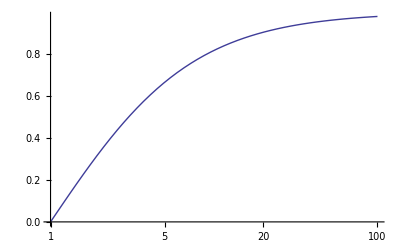

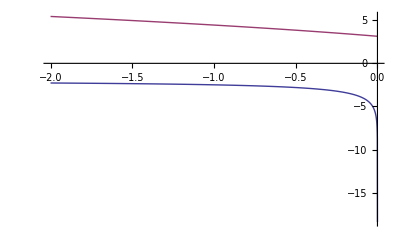

```mathematica
LogLinearPlot[-(1-b)/(1+b),{b,1,100}]
Plot[{Re@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]},Im@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]}},{r,-2,0}]
```

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> m2},m0-> 0,Assumptions-> {m2>0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)],2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)]}

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Expand@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> t},m0-> 0,Assumptions-> {t<0,m2>0,t-m2<0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-(m2 Log[m2])/(2 t)+Log[4 π]-Log[(m2-t)/(√m2)]+(m2 Log[(m2-t)/(√m2)])/t-Log[(√m2)/μ2],2-EulerGamma-2/ϵ+Log[4]-(m2 Log[m2])/t+(m2 Log[m2-t])/t-Log[(m2-t)/(π μ2)]}

### C_0

```mathematica
κ[x_,y_,z_]:=Sqrt[x^2+y^2+z^2-2(x y +y z + z x)];
Series[κ[x2,m2,m2],{x2,0,1}]
```

2 √-m2 √x2+O[x2]^(3/2)

```mathematica
sC0[μ2_][s,q2,0,m2_,m2_,m2_]:=Normal@Series[I Cϵ[m2,μ2]/(s-q2)(1/2 Log[χ]^2-1/2 Log[χq]^2-3Zeta[2])//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s],χq-> -(1-βq)/(1+βq),βq-> Sqrt[1-4m2/q2]},{ϵ,0,0}];
sC0[μ2_][0,q2,s,m2_,m2_,m2_]:=sC0[μ2][s,q2,0,m2,m2,m2]
sC0[μ2_][s,0,0,m2_,m2_,m2_]:=Normal@Series[I Cϵ[m2,μ2]/(s-q2)(1/2 Log[χ]^2-3Zeta[2])//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s]},{ϵ,0,0}];
sC0[μ2_][m2_,0,t,0,m2_,m2_]:=Normal@Series[I Cϵ[m2,μ2]/(t-m2)(Zeta[2]-PolyLog[2,t/m2]),{ϵ,0,0}];
sC0[μ2_][m2_,s,m2_,0,m2_,m2_]:=Normal@Series[(I Cϵ[m2,μ2]/(s β)(-2/ϵ Log[χ]-2Log[χ]Log[1-χ]-2PolyLog[2,χ]+1/2Log[χ]^2-4Zeta[2]))//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/s]},{ϵ,0,0}];
sC0[μ2_][t,M2_,q2,0,M2_,M2_]:=Normal@Series[I Cϵ[M2,μ2]((1/(6 Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))(-π^2+12 PolyLog[2,-((-M2+t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)])/(M2-t))]+6 PolyLog[2,(M2-q2+t-Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)])/(M2-q2+t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)])]+6 PolyLog[2,(q2 (-3 M2+q2-t-Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/(-3 M2 q2+q2^2-q2 t+Sqrt[q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))])]-6 PolyLog[2,(q2 (-3 M2+q2-t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/(-3 M2 q2+q2^2-q2 t+Sqrt[q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))])]+6 PolyLog[2,-((q2 (-3 M2+q2-t-Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/(3 M2 q2-q2^2+q2 t+Sqrt[q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))]))]-6 PolyLog[2,-((q2 (-3 M2+q2-t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/(3 M2 q2-q2^2+q2 t+Sqrt[q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))]))]-6 PolyLog[2,(M2^2-M2 (q2+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)])-t (-q2+t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/((M2-t) (M2-q2+t-Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))]-6 PolyLog[2,(M2^2-M2 (q2+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)])-t (-q2+t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))/((M2-t) (M2-q2+t+Sqrt[M2^2+(q2-t)^2-2 M2 (q2+t)]))])),{ϵ,0,0}];
```

#### Computing C_0(s,q.b2,0,m.b2,m.b2,m.b2)

```mathematica
Limit[-PolyLog[2,2/(1-b)]-PolyLog[2,2/(1+b)],b-> ∞,Assumptions-> {M2>0}]
Limit[-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))],q2-> 0,Assumptions-> {M2>0}]
```

0

0

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C},
p2[1]=p2[1,0]=s;
p2[2]=p2[2,0]=k2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
Print@Limit[αα,k2-> 0,Assumptions-> {s>0,s-q2>0}];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print[{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print@α[i];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print[{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print@Limit[y[0,i],k2->0,Assumptions-> {s>0,s-q2>0,M2>0}];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> {s>4M2>0,q2<0,s-q2>0}];
Print@C;
Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];
]
```

-q2+s

{0,1,2}

√(q2 (-4 M2+q2))

{(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

0

{1,2,0}

√(k2 (k2-4 M2))

{(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

q2/(q2-s)

{2,0,1}

√(s (-4 M2+s))

{(s+√(s (-4 M2+s)))/(2 s),(s-√(s (-4 M2+s)))/(2 s)}

1

(-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))])/(√(k2^2+q2^2+s^2-2 (k2 q2+k2 s+q2 s)))

1/(q2-s)(-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))]+PolyLog[2,(2 s)/(s-√(s (-4 M2+s)))]+PolyLog[2,(2 s)/(s+√(s (-4 M2+s)))])

-((-1+β^2) (-1+βq^2) (PolyLog[2,-2/(-1+β)]+PolyLog[2,2/(1+β)]-PolyLog[2,-2/(-1+βq)]-PolyLog[2,2/(1+βq)]))/(4 M2 (β^2-βq^2))

```mathematica
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],3Zeta@2-Log[x]^2/2}/.{x-> (1-b)/(1+b)}/.{b-> {.1,.3,.5,.7}}
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],-Log[xq]^2/2}/.{xq-> -(1-b)/(1+b)}/.{b-> {1.1,3.,5.,7.}}
```

{{4.91467-4.38675 ⅈ,4.7432-4.65146 ⅈ,4.33133-5.25895 ⅈ,3.43038-6.47055 ⅈ},{4.91467,4.7432,4.33133,3.43038}}

{{-4.63456,-0.240227,-0.082201,-0.0413805},{-4.63456,-0.240227,-0.082201,-0.0413805}}

```mathematica
Module[{K,iy,kx,iyx,r},
K=(1-β^2-4(1-x)x y)/(1-β^2);
Print@K;
iy=Integrate[1/K,y];
kx=FullSimplify[Limit[iy,y-> 1]-Limit[iy,y->0],Assumptions->{0<β<1}];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x];
r=FullSimplify[Limit[iyx,x->1]-Limit[iyx,x->0],Assumptions->{0<β<1}];
Print@Simplify[r*4m2/(s(1-β^2))];
]
```

(1-4 (1-x) x y-β^2)/(1-β^2)

((-1+β^2) (Log[-1+β^2]-Log[-1-4 (-1+x) x+β^2]))/(4 (-1+x) x)

-(m2 (-4 ArcTanh[β]^2+π (π-12 ⅈ Log[2]+2 ⅈ Log[1-β^2])))/(2 s)

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={0<ρ<1,ρq<0};
K=Simplify[(-a b *0-a c *s-b c q2+a m2+b m2+c m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq},Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(ρ ρq+4 x ((-1+y) ρ-y ρq)+4 x^2 (ρ-y ρ+y ρq))/(ρ ρq)

(ρ ρq (Log[ρ]-Log[(4 (-1+x) x+ρ) ρq]+Log[4 (-1+x) x+ρq]))/(4 (-1+x) x (ρ-ρq))

-1/(4 (ρ-ρq))ρ ρq (-Log[-1/2+x-(√(1-ρ))/2] Log[(2 (-1+x))/(-1+√(1-ρ))]-Log[x+1/2 (-1+√(1-ρ))] Log[(2-2 x)/(1+√(1-ρ))]+Log[1-x] Log[ρ]+Log[-1/2+x-(√(1-ρq))/2] Log[(2 (-1+x))/(-1+√(1-ρq))]+Log[x+1/2 (-1+√(1-ρq))] Log[(2-2 x)/(1+√(1-ρq))]+Log[-1+x] (Log[x+1/2 (-1+√(1-ρ))]+Log[-1/2+x-(√(1-ρ))/2]-Log[(-4 x+4 x^2+ρ) ρq])-Log[-1+x] (Log[x+1/2 (-1+√(1-ρq))]+Log[-1/2+x-(√(1-ρq))/2]-Log[-4 x+4 x^2+ρq])-PolyLog[2,(1-2 x+√(1-ρ))/(-1+√(1-ρ))]-PolyLog[2,(-1+2 x+√(1-ρ))/(1+√(1-ρ))]+PolyLog[2,(1-2 x+√(1-ρq))/(-1+√(1-ρq))]+PolyLog[2,(-1+2 x+√(1-ρq))/(1+√(1-ρq))])

-(ρ ρq (-4 ArcCoth[√(1-ρq)]^2+4 ArcTanh[√(1-ρ)]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[-(ρ (-2+2 √(1-ρq)+ρq))/ρq^2])))/(8 (ρ-ρq))

((-1+β^2) (-1+βq^2) (-4 ArcCoth[βq]^2+4 ArcTanh[β]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[(1-β^2)/(1+βq)^2])))/(8 (β^2-βq^2))

#### Computing C_0(m.b2,0,t,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=t;
p2[2,1]=k2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,t-M2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;
(*Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];*)
]
```

α = M2-t

i,j,k = {0,1,2}

α_i: √(k2 (k2-4 M2))

x_(i±) = {(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

y_(0  i) = -(M2+t)/(M2-t)

i,j,k = {1,2,0}

α_i: √((M2-t)^2)

x_(i±) = {(-M2+√((M2-t)^2)+t)/(2 t),-(M2+√((M2-t)^2)-t)/(2 t)}

y_(0  i) = -M2/t

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = 2

(π^2/3-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-2 PolyLog[2,(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)) (-1+(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) ((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))])/(√(k2^2+M2^2+t^2-2 (k2 M2+k2 t+M2 t)))

(π^2-12 PolyLog[2,2]-6 PolyLog[2,M2/t]+6 PolyLog[2,(M2+t)/M2]+6 PolyLog[2,(M2+t)/t])/(6 M2-6 t)

```mathematica
Module[{a,b,c,y},
a=π^2/6-2PolyLog[2,2]-PolyLog[2,1/z]+PolyLog[2,1+z]+PolyLog[2,1+1/z];
b=π^2/6-2PolyLog[2,2]-(-PolyLog[2,z]-π^2/6-1/2Log[-z]^2)+
(-PolyLog[2,-z]+π^2/6-Log[-z]Log[1+z])+
(-PolyLog[2,-1/z]+π^2/6-Log[-1/z]Log[1+1/z]);
c=π^2 5/6-2PolyLog[2,2]+PolyLog[2,z]+1/2Log[-z]^2+1/2Log[z]^2-Log[-z]Log[1+z]+Log[-z]Log[1+1/z];
y=-(Zeta[2]-PolyLog[2,z]);
Do[Print[{a,b,c,y}/.{z-> vz}],{vz,{-1.1,-3.,-5.,-7.}}];
]
```

{-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577}

{-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431}

{-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421}

{-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451}

```mathematica
π^2/3-Log[2]^2/2-Sum[1/(k^2 2^k),{k,1,∞}]
N@PolyLog[2,2]
N[π^2/4-I π Log@2]
```

π^2/4

2.4674-2.17759 ⅈ

2.4674-2.17759 ⅈ

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,t<0};
K=Simplify[(-a b *0-a c *m2-b c t+a 0+b m2+c m2)/m2,Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(t x (-1+x+y-x y)+m2 (1-2 x y+x^2 y))/m2

(m2 (Log[m2 (-1+x)^2]-Log[m2+t (-1+x) x]))/(x (t+m2 (-2+x)-t x))

1/(m2-t)m2 (2 Log[-m2 (-2+x)+t (-1+x)] Log[-1+x]-2 Log[2+(t (-1+x))/m2-x] Log[-1+x]-Log[-m2 (-2+x)+t (-1+x)] Log[m2 (-1+x)^2]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x]+Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x] Log[(2 t (t+m2 (-2+x)-t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x] Log[-(2 t (t+m2 (-2+x)-t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))]+Log[-m2 (-2+x)+t (-1+x)] Log[m2+t (-1+x) x]-2 PolyLog[2,((m2-t) (-1+x))/m2]+PolyLog[2,-((m2-t) (-t-√(t (-4 m2+t))+2 t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))+2 t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

#### Computing C_0(m.b2,s,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=s;
p2[2,1]=M2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
(*ϵ=0;*)
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,s>0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
(*C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;*)
]
```

α = √(s (-4 M2+s))

i,j,k = {0,1,2}

α_i: √3 √(-M2^2) (1+ⅈ M2 ϵ$13014)

x_(i±) = {(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2),(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)}

y_(0  i) = (-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))

i,j,k = {1,2,0}

α_i: √((M2-s)^2) (1+ⅈ s ϵ$13014)

x_(i±) = {(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s),-(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)}

y_(0  i) = -((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = (M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))

1/(√(2 M2^2+s^2-2 (M2^2+2 M2 s)))(π^2/3-2 PolyLog[2,(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)) (-1+(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))])

```mathematica
Module[{a,b,c,K,ix,ky,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,s>4m2,0<ρ<1,0<β<1,0<χ<1};
K=Simplify[(-a b *s-a c *m2-b c *m2+a m2+b *m2+c *0)/m2(*/.{s-> 4m2/ρ,q2-> 4m2/ρq}*),Assumptions->assum];
Print@K;
ix=Integrate[x K^(-1+ϵ/2),x,Assumptions->assum];
Print@ix;
ky=FullSimplify[Limit[ix,x-> 1,Assumptions->assum],Assumptions->assum];
ky=Simplify[Normal@Series[ky,{ϵ,0,0}]/.{s-> 4m2/ρ}/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}];
Print@ky;
iyx=Integrate[(-1/2)*2 ky,y,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,y->1,Assumptions->assum]-Limit[iyx,y->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[χ/(1-χ^2)/m2/.{χ-> (1-β)/(1+β)}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}];
Print@Collect[r/(χ/(1-χ^2)),ϵ,Simplify[#,Assumptions-> assum]&];
]
```

(x^2 (m2+s (-1+y) y))/m2

(x^2 ((x^2 (m2+s (-1+y) y))/m2)^(1/2 (-2+ϵ)))/ϵ

(χ (2+ϵ Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]))/(2 ϵ (χ-y (1+χ)^2+y^2 (1+χ)^2))

-1/(4 ϵ (-1+χ^2))χ (4 Log[y-χ+y χ]-2 ϵ Log[y-χ+y χ] Log[y-1/(1+χ)]-ϵ Log[y-1/(1+χ)]^2-2 ϵ Log[(-1+y+y χ)/(-1+χ)] Log[y-χ/(1+χ)]-2 ϵ Log[y-χ+y χ] Log[y-χ/(1+χ)]+ϵ Log[y-χ/(1+χ)]^2-4 Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-χ/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[(χ-y (1+χ))/(-1+χ)]+2 ϵ Log[y-χ+y χ] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]-2 ϵ Log[1-y (1+χ)] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]+2 ϵ PolyLog[2,(-1+y+y χ)/(-1+χ)]-2 ϵ PolyLog[2,(χ-y (1+χ))/(-1+χ)])

1/(2 ϵ (-1+χ^2))χ (π (4 ⅈ+π ϵ)+Log[χ] (4+2 ϵ Log[1-χ]-ϵ Log[χ])-2 ⅈ π ϵ Log[χ/(1+χ)]+2 ϵ PolyLog[2,1/(1-χ)]-2 ϵ PolyLog[2,χ/(-1+χ)])

1/(√(1-(4 m2)/s) s)

(-2 ⅈ π-2 Log[χ])/ϵ+1/2 (-π^2-2 Log[1-χ] Log[χ]+Log[χ]^2+2 ⅈ π Log[χ/(1+χ)]-2 PolyLog[2,1/(1-χ)]+2 PolyLog[2,χ/(-1+χ)])

```mathematica
Module[{a,b,z},
(*a=PolyLog[2,1/(1-x)];
b=PolyLog[2,x]-π^2/3+Log[x]Log[1-x]-1/2Log[x-1]^2;
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
a=PolyLog[2,x/(x-1)];
b=-PolyLog[2,1/(1-x)]+π^2/6+Log[1-x](Log[x]-Log[x-1]);
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];*)
a=-2PolyLog[2,1/(1-x)]+2PolyLog[2,x/(x-1)];
b=-4PolyLog[2,x]-π^2/3-2Log[x]Log[1-x];
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
]
```

{-4.18554+0.662 ⅈ,-4.18554}

{-5.45324+2.24105 ⅈ,-5.45324}

{-6.57974+4.35517 ⅈ,-6.57974}

{-7.70623+7.56478 ⅈ,-7.70623}

#### Computing C_0(t,q.b2,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=t;
p2[2]=p2[2,0]=M2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,q2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
C=Simplify[C,Assumptions-> ass];
Print@C;
Print@Simplify[Limit[C,q2-> 0,Assumptions-> ass],Assumptions-> ass];
]
```

α = √(M2^2+(q2-t)^2-2 M2 (q2+t))

i,j,k = {0,1,2}

α_i: √(q2 (-4 M2+q2))

x_(i±) = {(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

y_(0  i) = (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 √(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {1,2,0}

α_i: 0

x_(i±) = {0,0}

y_(0  i) = (M2-t)/(√(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {2,0,1}

α_i: √((M2-t)^2)

x_(i±) = {(M2+t+√((-M2+t)^2))/(2 t),(M2+t-√((-M2+t)^2))/(2 t)}

y_(0  i) = (M2 (-M2+q2)+t (-q2+t)+(M2+t) √(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 t √(M2^2+(q2-t)^2-2 M2 (q2+t)))

1/(6 √(M2^2+(q2-t)^2-2 M2 (q2+t)))(-π^2+12 PolyLog[2,-(-M2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-t)]+6 PolyLog[2,(M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))]+6 PolyLog[2,(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]+6 PolyLog[2,-(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,-(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))])

-(π^2-6 PolyLog[2,t/M2])/(6 M2-6 t)

### D_0

#### Computing D_0(m.b2,0,q.b2,m.b2,t,s,0,m.b2,m.b2,m.b2)

```mathematica
Module[{
assum,params,p,a,b,c,d,Jac,K,pK,j,
i1,k1,uk1,lk1,
i2a,k2a,k2aCounter,k2aSub,i3aSub,resaSub,i3aCounter,resaCounter,resa,
i2b,uk1p,t,k2b,i3b,resb,i3a,
k2ba,k2baCounter,k2baSub,i3baSub,resbaSub,i3baCounter,resbaCounter,resba,
k2bb,k2bbCounter,k2bbSub,i3bbSub,resbbSub,i3bbCounter,resbbCounter,resbb,
res,Pϵ
},
(* setup data *)
Jac=6x^2 y;
assum={m2>0,s>4m2,q2<0,s-q2>0,t<0,0<ρ<1,ρq<0,0<β<1,0<χ<1,tTil>0,βq>1};
K=Simplify[(-a b *m2-a c *t-a d*m2-b c*0-b d*s-c d q2+a*0+b *m2+c*m2+d*m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq,t-> m2(1-tTil)},Assumptions->assum];
(* choose parameterization *)
params=Permute[{x y z,x y(1-z),x(1-y),(1-x)},AlternatingGroup[4]];
p=params[[11]];
pK=K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]};
(* integrate z *)
i1=Integrate[Jac*pK^(-2+ϵ/2),z,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
uk1=FullSimplify[Limit[i1,z-> 1,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
lk1=FullSimplify[Limit[i1,z-> 0,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
k1=Simplify[uk1-lk1,Assumptions->assum];
Print["{uk1,lk1} = ",{uk1,lk1}];
Print[];
(* split x integration: a *)
i2a=Integrate[lk1,x,Assumptions->assum];
Print["i2a = ",i2a];
k2a=Limit[i2a,x-> 1,Assumptions->assum];
k2a=k2a/.{Hypergeometric2F1[1,ϵ,1+ϵ,z_]:> 1-ϵ Log[Simplify[1-z,Assumptions->assum]]-ϵ^2PolyLog[2,Simplify[z,Assumptions->assum]]};
k2a=Normal@Series[k2a,{ϵ,0,0}];
i3a=Integrate[k2a,y];
resa=Simplify[(Limit[i3a,y-> 1,Assumptions->assum]-Limit[i3a,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
Print["resa = ",resa];
(*k2aCounter=(12 (1-ϵ Log[(4 (-1+y) (ρ-ρq))/(tTil ρ ρq)]-ϵ^2 π^2/6))/(tTil (-2+ϵ) ϵ);
k2aSub=Simplify[Normal@Series[k2a-k2aCounter,{ϵ,0,0}],Assumptions->assum];
i3aSub=Integrate[k2aSub,y,Assumptions->assum];
resaSub=Simplify[Limit[i3aSub,y->1,Assumptions->assum]-Limit[i3aSub,y->0,Assumptions->assum]/.{ρ-> 1-β^2},Assumptions->assum];
i3aCounter=Integrate[k2aCounter,y,Assumptions->assum];
resaCounter=Normal@Series[Limit[i3aCounter,y-> 1,Assumptions->assum]-Limit[i3aCounter,y-> 0,Assumptions->assum],{ϵ,0,0}];
resa=Collect[resaSub+resaCounter,ϵ,FullSimplify[#/.{ρ-> 1-β^2,ρq-> 1-βq^2}/.{β-> (1-χ)/(1+χ)},Assumptions->assum]&];
Print["resa = ",resa];*)
Print[];
(* part b *)
uk1=Limit[uk1,ϵ->0,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
i2b=Integrate[uk1,x];
k2b=Simplify[Limit[i2b,x-> 1,Assumptions->assum]-Limit[i2b,x-> 0,Assumptions->assum],Assumptions->assum];
i3b=Integrate[k2b,y];
resb=Simplify[(Limit[i3b,y-> 1,Assumptions->assum]-Limit[i3b,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
Print["resb = ",resb];
Print[];
(* join elements *)
Pϵ=1/6(1-ϵ/2+ϵ^2/8 Zeta[2]);
res=Collect[Normal@Series[Pϵ(resa+resb),{ϵ,0,0}],ϵ,Simplify[TrigToExp@#,Assumptions->assum]&];
Print["res = ",res];
(*uk1p=(12  ρ ρq (((tTil y ρq+x (4 y^2+ρq-y (4+tTil ρq))))/ρq)^(1/2 (-2+ϵ)))/((-2+ϵ) (tTil ρ ρq+x (-4 (-1+y) ρq+ρ (-4+4 y-tTil ρq))));
i2b=Integrate[uk1p,x,Assumptions->assum];
Print["i2b = ",i2b];
k2ba=Simplify[(Limit[i2b,x-> 1])/.{Hypergeometric2F1[1,ϵ/2,(2+ϵ)/2,z_]:> 1-2ϵ Log[Simplify[1-z,Assumptions->assum]]-4ϵ^2PolyLog[2,Simplify[z,Assumptions->assum]]},Assumptions->assum];
k2bb=Simplify[(Limit[-i2b,x-> 0])/.{Hypergeometric2F1[1,ϵ/2,(2+ϵ)/2,z_]:> 1-2ϵ Log[Simplify[1-z,Assumptions->assum]]-4ϵ^2PolyLog[2,Simplify[z,Assumptions->assum]]},Assumptions->assum];
Print["k2ba = ",k2ba];
Print["k2bb = ",k2bb];
(* split y integration: ba *)
k2baCounter=-((24 (-1+2 ϵ Log[-(4 (y-1) (ρ-ρq) (tTil-1))/(tTil ρ ρq)]+4 ϵ^2 π^2/6))/(tTil (-2+ϵ) ϵ ));
(*Print["k2ba ~ ",Series[k2ba,{y,1,0},Assumptions->assum~Join~{0<y<1}]];
Print["k2baCounter ~ ",Series[k2baCounter,{y,1,0},Assumptions->assum~Join~{0<y<1}]];*)
k2baSub=Simplify[Normal@Series[k2ba-k2baCounter,{ϵ,0,0}],Assumptions->assum];
i3baSub=Integrate[k2baSub,y,Assumptions->assum];
resbaSub=Simplify[Limit[i3baSub,y->1,Assumptions->assum]-Limit[i3baSub,y->0,Assumptions->assum]/.{ρ-> 1-β^2},Assumptions->assum];
(*Print@resbaSub;*)
i3baCounter=Integrate[k2baCounter,y,Assumptions->assum];
resbaCounter=Normal@Series[Limit[i3baCounter,y-> 1,Assumptions->assum]-Limit[i3baCounter,y-> 0,Assumptions->assum],{ϵ,0,0}];
(*Print@resbaCounter;*)
resba=Collect[resbaSub+resbaCounter,ϵ,Simplify[#/.{ρ-> 1-β^2,ρq-> 1-βq^2}/.{β-> (1-χ)/(1+χ)},Assumptions->assum]&];
Print["resba = ",resba];
Print[];
(* part bb *)
(*Print["k2bb ~ ",Series[k2bb,{y,0,0},Assumptions->assum~Join~{0<y<1}]];*)
k2bbCounter=-24(tTil y)^(ϵ/2)/(tTil(ϵ-2)ϵ);
k2bbSub=Simplify[Normal@Series[k2bb-k2bbCounter,{ϵ,0,0}],Assumptions->assum];
i3bbSub=Integrate[k2bbSub,y,Assumptions->assum];
resbbSub=Simplify[Limit[i3bbSub,y->1,Assumptions->assum]-Limit[i3bbSub,y->0,Assumptions->assum]/.{ρ-> 1-β^2},Assumptions->assum];
(*Print@resbbSub;*)
i3bbCounter=Integrate[k2bbCounter,y,Assumptions->assum];
i3bbCounter=Normal@Series[i3bbCounter,{ϵ,0,0},Assumptions->assum];
resbbCounter=Limit[i3bbCounter,y-> 1,Assumptions->assum]-Limit[i3bbCounter,y-> 0,Assumptions->assum];
(*Print@resbbCounter;*)
resbb=Collect[resbbSub+resbbCounter,ϵ,Simplify[#/.{ρ-> 1-β^2,ρq-> 1-βq^2}/.{β-> (1-χ)/(1+χ)},Assumptions->assum]&];
Print["resbb = ",resbb];
(*resbb=Collect[resbb,ϵ,FullSimplify[#,Assumptions->assum]&];
Print["resbb = ",resbb];*)
(* join elements *)
Pϵ=1/6(1-ϵ/2+ϵ^2/8 Zeta[2]);
res=Collect[Normal@Series[Pϵ(resa+resba+resbb),{ϵ,0,0}],ϵ,Simplify[TrigToExp@#,Assumptions->assum]&];
Print["res = ",res];*)
]
```

{uk1,lk1} = {(12 x ρ ρq ((x (tTil y ρq+x (ρq+y (-4+4 y-tTil ρq))))/ρq)^(1/2 (-2+ϵ)))/((-2+ϵ) (4 x (-1+y) ρ+tTil ρ ρq-x (-4+4 y+tTil ρ) ρq)),(12 x ρ^(2-ϵ/2) (x^2 (4 (-1+y) y+ρ))^(1/2 (-2+ϵ)) ρq)/((-2+ϵ) (4 x (-1+y) ρ+tTil ρ ρq-x (-4+4 y+tTil ρ) ρq))}

i2a = (12 x^2 ρ^(1-ϵ/2) (x^2 (4 (-1+y) y+ρ))^(1/2 (-2+ϵ)) Hypergeometric2F1[1,ϵ,1+ϵ,(x (4 (-1+y) ρq+ρ (4-4 y+tTil ρq)))/(tTil ρ ρq)])/(tTil (-2+ϵ) ϵ)

resa = 1/(4 tTil β ϵ)3 (-1+β^2) (4 ⅈ π+2 ⅈ π ϵ+π^2 ϵ+ϵ Log[(1-β)/2]^2+ⅈ π ϵ Log[1-β]+ϵ Log[(1-β)/2] Log[4 β^2]+4 Log[(1-β)/(1+β)]+2 ϵ Log[(1-β)/(1+β)]-2 ⅈ π ϵ Log[(1-β)/(1+β)]-ϵ Log[(1-β)/2] Log[(1-β)/(1+β)]+2 ϵ Log[1-β] Log[(1+β)/2]-ϵ Log[4 β^2] Log[(1+β)/2]-ϵ Log[(1-β)/(1+β)] Log[(1+β)/2]-ϵ Log[(1+β)/2]^2-ⅈ π ϵ Log[1+β]-2 ϵ Log[(1-β)/2] Log[1+β]-ⅈ π ϵ Log[1/4 (1-β^2)]-ϵ Log[(1-β)/(1+β)] Log[1/4 (1-β^2)]-4 ϵ Log[1-β] Log[(4 (β^2-βq^2))/(tTil (-1+β^2) (-1+βq^2))]+4 ϵ Log[1+β] Log[(4 (β^2-βq^2))/(tTil (-1+β^2) (-1+βq^2))]+2 ϵ PolyLog[2,-2/(-1+β)]-2 ϵ PolyLog[2,(-1+β)/(2 β)]-2 ϵ PolyLog[2,2/(1+β)]+2 ϵ PolyLog[2,(1+β)/(2 β)])

resb = 1/(2 tTil β)3 (-1+β^2) (ⅈ π Log[1-β]-ⅈ π Log[(1-β)/(1+β)]-ⅈ π Log[1+β]+ⅈ π Log[(1+β)/(1-β)]+Log[(1-β)/(1+β)] Log[1-β^2]-Log[(1+β)/(1-β)] Log[1-β^2]+ⅈ π Log[(-1+β)/(β-βq)]+2 Log[(-1+β)/(β-βq)] Log[1/2 (-1+βq)]+2 Log[1-β] Log[(1+βq)/2]-2 Log[1+β] Log[(1+βq)/2]+ⅈ π Log[-β+βq]+2 Log[(1+βq)/2] Log[-β+βq]-ⅈ π Log[(1+β)/(β+βq)]-2 Log[1/2 (-1+βq)] Log[(1+β)/(β+βq)]-ⅈ π Log[β+βq]-2 Log[(1+βq)/2] Log[β+βq]-2 ⅈ π Log[1/4 (-1+βq^2)]-2 Log[(1-β)/(1+β)] Log[1/4 (-1+βq^2)]+2 ⅈ π Log[-1+βq^2]+2 Log[(1-β)/(1+β)] Log[-1+βq^2]-2 Log[1-β] Log[4 (-β^2+βq^2)]+2 Log[1+β] Log[4 (-β^2+βq^2)]+2 PolyLog[2,-2/(-1+β)]-2 PolyLog[2,2/(1+β)]+2 PolyLog[2,(-1+βq)/(-β+βq)]-2 PolyLog[2,(1+βq)/(-β+βq)]-2 PolyLog[2,(-1+βq)/(β+βq)]+2 PolyLog[2,(1+βq)/(β+βq)])

res = ((-1+β^2) (ⅈ π+Log[(1-β)/(1+β)]))/(2 tTil β ϵ)+1/(8 tTil β)(-1+β^2) (π^2+5 ⅈ π Log[4]-ⅈ π Log[1-β]+Log[4] Log[1-β]-2 Log[256] Log[1-β]+4 Log[tTil] Log[1-β]+2 Log[1-β] Log[β]+ⅈ π Log[1+β]-Log[4] Log[1+β]+Log[65536] Log[1+β]-4 Log[tTil] Log[1+β]-2 Log[β] Log[1+β]-ⅈ π Log[1-β^2]+7 Log[1-β] Log[1-β^2]-7 Log[1+β] Log[1-β^2]+4 Log[1-β] Log[-1+βq]-4 Log[1+β] Log[-1+βq]+4 Log[1-β] Log[1+βq]-4 Log[1+β] Log[1+βq]-4 Log[-1+βq] Log[-β+βq]+4 Log[1+βq] Log[-β+βq]+4 Log[-1+βq] Log[β+βq]-4 Log[1+βq] Log[β+βq]+4 Log[1-β] Log[-1+βq^2]-4 Log[1+β] Log[-1+βq^2]-8 Log[1-β] Log[-β^2+βq^2]+8 Log[1+β] Log[-β^2+βq^2]+6 PolyLog[2,-2/(-1+β)]-2 PolyLog[2,(-1+β)/(2 β)]-6 PolyLog[2,2/(1+β)]+2 PolyLog[2,(1+β)/(2 β)]-4 PolyLog[2,-(1+βq)/(β-βq)]+4 PolyLog[2,(-1+βq)/(-β+βq)]-4 PolyLog[2,(-1+βq)/(β+βq)]+4 PolyLog[2,(1+βq)/(β+βq)])

```mathematica
Simplify[(χ)/(tTil (-1+χ) (1+χ))/.{χ-> (1-β)/(1+β),tTil-> -t1/m2}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}]
```

m2^2/(√(1-(4 m2)/s) s t1)

```mathematica
Module[{i,l,u},
i=Integrate[2x^(-1+ϵ)(1-y)^(-1+ϵ/2)(1+(tTil-1)y)^(-1+ϵ/2)/((ϵ-2)(sTil(1-x)+tTil x (1-y))),x];
Print@Series[i,{x,0,0},Assumptions->assum];
Print@Series[i,{x,1,0},Assumptions->assum];
Print@Series[i,{y,0,0},Assumptions->assum];
Print@Series[i,{y,1,0},Assumptions->assum];
Print@i;
l=Limit[i,x-> 0];
Print@l;
Print@Limit[Simplify[i/.{Hypergeometric2F1[1,1+ϵ,2+ϵ,z_]:> - Log[1-z]/z-ϵ/z (Log[1-z]+PolyLog[2,z])}],x-> 0];
u=Limit[i,x-> 1];
Print@u;
Print@Simplify[u/.{Hypergeometric2F1[1,1+ϵ,2+ϵ,z_]:> - Log[1-z]/z-ϵ/z (Log[1-z]+PolyLog[2,z])}];
]
```

x^ϵ ((2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil+sTil ϵ))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[x]^1)

(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+(sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(sTil-tTil+tTil y)/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[x-1]^1

(2 x^ϵ (sTil (1+ϵ)+(sTil-tTil) x ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,((sTil-tTil) x)/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[y]^1

(1-y)^(-1+ϵ/2) ((2 tTil^(-1+ϵ/2) x^ϵ (1+ϵ+x ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,x]))/(sTil (-2+ϵ) ϵ (1+ϵ))+O[y-1]^1)

(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+x (sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(x (sTil+tTil (-1+y)))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))

Limit[(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+x (sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(x (sTil+tTil (-1+y)))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ)),x→0]

Limit[-(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) ((1+ϵ) (-1+ϵ Log[1-(x (sTil+tTil (-1+y)))/sTil])+ϵ^2 PolyLog[2,(x (sTil+tTil (-1+y)))/sTil]))/(sTil (-2+ϵ) ϵ (1+ϵ)),x→0]

(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+(sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(sTil+tTil (-1+y))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))

-(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) ((1+ϵ) (-1+ϵ Log[-(tTil (-1+y))/sTil])+ϵ^2 PolyLog[2,(sTil+tTil (-1+y))/sTil]))/(sTil (-2+ϵ) ϵ (1+ϵ))

```mathematica
(* z *)
```

b$173379-a$173379 b$173379+c$173379+d$173379-a$173379 d$173379-(a$173379 c$173379)/tOvm2-(4 b$173379 d$173379)/ρ-(4 c$173379 d$173379)/ρq

j = 1

pK = 1-x+x (1-y)+x y (1-z)-(1-x) x y z-(x^2 (1-y) y z)/tOvm2-x^2 y^2 (1-z) z-(4 (1-x) x y (1-z))/ρ-(4 (1-x) x (1-y))/ρq

-(24 tOvm2^3 x^6 y^5 ρ^3 ρq^2 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 z^2 ρ ρq+z (4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))])/((-2+ϵ) (16 tOvm2^2 x ρ^2-16 tOvm2^2 x^2 ρ^2-16 tOvm2^2 x y ρ^2+16 tOvm2^2 x^2 y ρ^2+16 tOvm2^2 ρq-32 tOvm2^2 x ρq+16 tOvm2^2 x^2 ρq-16 tOvm2^2 ρ ρq-8 tOvm2 x ρ ρq+24 tOvm2^2 x ρ ρq+8 tOvm2 x^2 ρ ρq-8 tOvm2^2 x^2 ρ ρq+8 tOvm2 x y ρ ρq+8 tOvm2^2 x y ρ ρq-8 tOvm2 x^2 y ρ ρq-8 tOvm2^2 x^2 y ρ ρq+4 tOvm2 x ρ^2 ρq-4 tOvm2^2 x ρ^2 ρq+x^2 ρ^2 ρq-2 tOvm2 x^2 ρ^2 ρq+tOvm2^2 x^2 ρ^2 ρq-4 tOvm2 x y ρ^2 ρq+4 tOvm2^2 x y ρ^2 ρq-2 x^2 y ρ^2 ρq+4 tOvm2 x^2 y ρ^2 ρq-2 tOvm2^2 x^2 y ρ^2 ρq+x^2 y^2 ρ^2 ρq-2 tOvm2 x^2 y^2 ρ^2 ρq+tOvm2^2 x^2 y^2 ρ^2 ρq) (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+2 tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-2 tOvm2 x^2 y^2 z ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2)))

j = 2

pK = 1-x+x (1-y)+x y (1-z)-((1-x) x y z)/tOvm2-x^2 (1-y) y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y (1-z))/ρ-(4 (1-x) x y (1-z))/ρq

(24 tOvm2^3 x^6 y^5 ρ^3 ρq^3 (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 z^2 ρ ρq+z (-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq)))^(1/2 (-4+ϵ)) ((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))^((4-ϵ)/2) (((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))^((4-ϵ)/2+ϵ/2) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))^((4-ϵ)/2+ϵ/2) (1+(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(tOvm2 x y ρ (-4+ρq)-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq-(-1+x) x y ρ ρq+tOvm2 x^2 y ρ (4+ρq)+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))])/((-2+ϵ) (-16 tOvm2^2 ρ^2+32 tOvm2^2 x ρ^2-16 tOvm2^2 x^2 ρ^2-32 tOvm2^2 x ρ ρq+32 tOvm2^2 x^2 ρ ρq+32 tOvm2^2 x y ρ ρq-32 tOvm2^2 x^2 y ρ ρq+8 tOvm2 ρ^2 ρq+8 tOvm2^2 ρ^2 ρq-16 tOvm2 x ρ^2 ρq+8 tOvm2 x^2 ρ^2 ρq-8 tOvm2^2 x^2 ρ^2 ρq-16 tOvm2^2 x y ρ^2 ρq+16 tOvm2^2 x^2 y ρ^2 ρq-16 tOvm2^2 x^2 ρq^2+32 tOvm2^2 x^2 y ρq^2-16 tOvm2^2 x^2 y^2 ρq^2+8 tOvm2 x ρ ρq^2+8 tOvm2^2 x ρ ρq^2-8 tOvm2 x^2 ρ ρq^2+8 tOvm2^2 x^2 ρ ρq^2-8 tOvm2 x y ρ ρq^2-8 tOvm2^2 x y ρ ρq^2+8 tOvm2 x^2 y ρ ρq^2-24 tOvm2^2 x^2 y ρ ρq^2+16 tOvm2^2 x^2 y^2 ρ ρq^2-ρ^2 ρq^2-2 tOvm2 ρ^2 ρq^2+3 tOvm2^2 ρ^2 ρq^2+2 x ρ^2 ρq^2-2 tOvm2^2 x ρ^2 ρq^2-x^2 ρ^2 ρq^2+2 tOvm2 x^2 ρ^2 ρq^2-tOvm2^2 x^2 ρ^2 ρq^2) (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq-2 tOvm2 x^2 y^2 z ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x y ρ+4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y ρq+4 tOvm2 x^2 y^2 ρq+tOvm2 ρ ρq)+(-tOvm2 x y ρ (-4+ρq)+4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq+(-1+x) x y ρ ρq-tOvm2 x^2 y ρ (4+ρq))^2)))

j = 3

pK = 1-x+x (1-y)+x y (1-z)-(1-x) x y z-x^2 (1-y) y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 x^2 (1-y) y (1-z))/ρq

-(24 x^6 y^5 ρ^2 ρq^3 (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq+x^2 y^2 z^2 ρ ρq+z (4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq-√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (1+(z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))/(-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq-√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2))+1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))/(-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq-√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2))+1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-tOvm2 x^2 y^2 ρ (-4+ρq)+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))])/((-2+ϵ) (16 tOvm2^2 x^2 ρ-32 tOvm2^2 x^2 y ρ+16 tOvm2^2 x^2 y^2 ρ-16 tOvm2^2 x ρ ρq+16 tOvm2^2 x y ρ ρq+8 tOvm2 x^2 y ρ ρq+8 tOvm2^2 x^2 y ρ ρq-8 tOvm2 x^2 y^2 ρ ρq-8 tOvm2^2 x^2 y^2 ρ ρq+16 tOvm2 x ρq^2-16 tOvm2 x^2 ρq^2-16 tOvm2 x y ρq^2+16 tOvm2 x^2 y ρq^2-4 tOvm2 ρ ρq^2+4 tOvm2^2 ρ ρq^2+4 tOvm2 x y ρ ρq^2-4 tOvm2^2 x y ρ ρq^2+x^2 y^2 ρ ρq^2-2 tOvm2 x^2 y^2 ρ ρq^2+tOvm2^2 x^2 y^2 ρ ρq^2) (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ+2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq-2 x^2 y^2 z ρ ρq+√(-4 x^2 y^2 ρ ρq (-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 y^2 ρ-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρ (-4+ρq)-2 tOvm2 x y ρ ρq-x^2 y^2 ρ ρq)^2)))

j = 4

pK = 1-x+x (1-y)-((1-x) x y (1-z))/tOvm2-x^2 (1-y) y (1-z)+x y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y z)/ρ-(4 (1-x) x (1-y))/ρq

(24 tOvm2^3 x^6 y^5 ρ^3 ρq^2 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 (-1+z)^2 ρ ρq+(-1+z) (4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq))^(1/2 (-4+ϵ)) (-1+z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (-1+z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))^((4-ϵ)/2+ϵ/2) (x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))^((4-ϵ)/2) ((x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(-1+z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(-1+z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 (-1+y) y ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))])/((-2+ϵ) (-16 tOvm2^2 x ρ^2+16 tOvm2^2 x^2 ρ^2+16 tOvm2^2 x y ρ^2-16 tOvm2^2 x^2 y ρ^2-16 tOvm2^2 x^2 ρq+32 tOvm2^2 x^2 y ρq-16 tOvm2^2 x^2 y^2 ρq+8 tOvm2 x ρ ρq+8 tOvm2^2 x ρ ρq-8 tOvm2 x^2 ρ ρq+8 tOvm2^2 x^2 ρ ρq-8 tOvm2 x y ρ ρq-8 tOvm2^2 x y ρ ρq+8 tOvm2 x^2 y ρ ρq-24 tOvm2^2 x^2 y ρ ρq+16 tOvm2^2 x^2 y^2 ρ ρq-ρ^2 ρq-2 tOvm2 ρ^2 ρq+3 tOvm2^2 ρ^2 ρq+2 x ρ^2 ρq-2 tOvm2^2 x ρ^2 ρq-x^2 ρ^2 ρq+2 tOvm2 x^2 ρ^2 ρq-tOvm2^2 x^2 ρ^2 ρq) (4 tOvm2 x^2 y ρq-4 tOvm2 x^2 y^2 ρq-x y ρ ρq-tOvm2 x y ρ ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-2 tOvm2 x^2 y^2 (-1+z) ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ+4 tOvm2 x^2 (-1+y) y ρq+tOvm2 ρ ρq)+(4 tOvm2 x^2 (-1+y) y ρq+x y ρ ρq+tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq)^2)))

j = 5

pK = 1-x+x (1-y)-(1-x) x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 (1-x) x y z)/ρq

-(24 x^6 y^5 ρ^2 ρq^3 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+x^2 y^2 z^2 ρ ρq+z (4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))^((4-ϵ)/2+ϵ/2) (z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))^((4-ϵ)/2+ϵ/2) (1+(z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))/(-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq)))+1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq)))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))/(-1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq)))+1/(2 x^2 y^2 ρ ρq)(-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ (-2+ρq)+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))])/((-2+ϵ) (16 tOvm2^2 ρ-32 tOvm2^2 x ρ+16 tOvm2^2 x^2 ρ-16 tOvm2^2 ρ ρq+16 tOvm2^2 x ρ ρq+8 tOvm2 x y ρ ρq+8 tOvm2^2 x y ρ ρq-8 tOvm2 x^2 y ρ ρq-8 tOvm2^2 x^2 y ρ ρq+16 tOvm2 x ρq^2-16 tOvm2 x^2 ρq^2-16 tOvm2 x y ρq^2+16 tOvm2 x^2 y ρq^2-4 tOvm2 ρ ρq^2+4 tOvm2^2 ρ ρq^2+4 tOvm2 x y ρ ρq^2-4 tOvm2^2 x y ρ ρq^2+x^2 y^2 ρ ρq^2-2 tOvm2 x^2 y^2 ρ ρq^2+tOvm2^2 x^2 y^2 ρ ρq^2) (4 tOvm2 x y ρ-4 tOvm2 x^2 y ρ-2 tOvm2 x y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-2 x^2 y^2 z ρ ρq+√((4 tOvm2 x^2 y ρ+2 tOvm2 x y ρ (-2+ρq)-x^2 y^2 ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-4 x^2 y^2 ρ ρq (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y (-2+ρ) ρq+tOvm2 ρ ρq+tOvm2 x^2 y^2 ρ ρq))))

j = 6

pK = 1-x+x (1-y)-(1-x) x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 y^2 (1-z) z-(4 (1-x) x y z)/ρ-(4 x^2 (1-y) y z)/ρq

-(24 tOvm2^3 x^6 y^5 ρ^3 ρq^3 (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 z^2 ρ ρq+z (2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))))^(1/2 (-4+ϵ)) (x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))^((4-ϵ)/2) ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))-√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))^((4-ϵ)/2+ϵ/2) (z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))^((4-ϵ)/2+ϵ/2) (1+(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))-√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))/(-1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))-√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2))+1/(2 tOvm2 x^2 y^2 ρ ρq)(-2 tOvm2 x y (-2+ρ) ρq-x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq))+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))])/((-2+ϵ) (16 tOvm2^2 x^2 ρ^2-32 tOvm2^2 x^2 y ρ^2+16 tOvm2^2 x^2 y^2 ρ^2+32 tOvm2^2 x ρ ρq-32 tOvm2^2 x^2 ρ ρq-32 tOvm2^2 x y ρ ρq+32 tOvm2^2 x^2 y ρ ρq-16 tOvm2^2 x ρ^2 ρq-8 tOvm2 x^2 ρ^2 ρq+8 tOvm2^2 x^2 ρ^2 ρq+16 tOvm2^2 x y ρ^2 ρq+16 tOvm2 x^2 y ρ^2 ρq-8 tOvm2 x^2 y^2 ρ^2 ρq-8 tOvm2^2 x^2 y^2 ρ^2 ρq+16 tOvm2^2 ρq^2-32 tOvm2^2 x ρq^2+16 tOvm2^2 x^2 ρq^2-16 tOvm2^2 ρ ρq^2-8 tOvm2 x ρ ρq^2+24 tOvm2^2 x ρ ρq^2+8 tOvm2 x^2 ρ ρq^2-8 tOvm2^2 x^2 ρ ρq^2+8 tOvm2 x y ρ ρq^2+8 tOvm2^2 x y ρ ρq^2-8 tOvm2 x^2 y ρ ρq^2-8 tOvm2^2 x^2 y ρ ρq^2+4 tOvm2 x ρ^2 ρq^2-4 tOvm2^2 x ρ^2 ρq^2+x^2 ρ^2 ρq^2-2 tOvm2 x^2 ρ^2 ρq^2+tOvm2^2 x^2 ρ^2 ρq^2-4 tOvm2 x y ρ^2 ρq^2+4 tOvm2^2 x y ρ^2 ρq^2-2 x^2 y ρ^2 ρq^2+4 tOvm2 x^2 y ρ^2 ρq^2-2 tOvm2^2 x^2 y ρ^2 ρq^2+x^2 y^2 ρ^2 ρq^2-2 tOvm2 x^2 y^2 ρ^2 ρq^2+tOvm2^2 x^2 y^2 ρ^2 ρq^2) (4 tOvm2 x^2 y ρ-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq-4 tOvm2 x^2 y ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq-2 tOvm2 x^2 y^2 z ρ ρq+√(-4 tOvm2 x^2 y^2 ρ ρq (tOvm2 ρ ρq-2 tOvm2 x y ρ ρq-x^2 y ρ ρq+tOvm2 x^2 y ρ ρq+x^2 y^2 ρ ρq)+(2 tOvm2 x y (-2+ρ) ρq+x^2 y ρ ρq-x^2 y^2 ρ ρq-tOvm2 x^2 y (-4 ρq+ρ (4+y (-4+ρq)+ρq)))^2)))

j = 7

pK = 1-x-(1-x) x (1-y)+x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 (1-y) y z-(4 (1-x) x y z)/ρ-(4 (1-x) x y (1-z))/ρq

(12 tOvm2 x ρ ρq ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(tOvm2 ρ ρq))^(1/2 (-2+ϵ)))/((-2+ϵ) (-x (-1+y) ρ ρq+tOvm2 (4 (-1+x) ρq+ρ (4+x (-4+(-1+y) ρq)))))

j = 8

pK = 1-x-((1-x) x (1-y))/tOvm2+x y (1-z)-x^2 (1-y) y (1-z)+x y z-x^2 (1-y) y z-(4 x^2 y^2 (1-z) z)/ρ-(4 (1-x) x y z)/ρq

(24 tOvm2^2 x^6 y^5 ρq^3 (4 tOvm2 x^2 y^2 z^2 ρq+tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq+z (-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq)))^(1/2 (-4+ϵ)) (x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))^((4-ϵ)/2) ((x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)-√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq))^((4-ϵ)/2+ϵ/2) (z-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)+√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq))^((4-ϵ)/2+ϵ/2) (1+(z-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)+√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq))/(-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)-√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq)+(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)+√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq)))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)+√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq))/(-(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)-√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq)+(4 tOvm2 x y ρ-4 tOvm2 x^2 y (ρ-y ρq)+√(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2))/(8 tOvm2 x^2 y^2 ρq))])/((-2+ϵ) (-tOvm2 ρ^2+2 tOvm2 x ρ^2-tOvm2 x^2 ρ^2-2 tOvm2 x y ρ ρq+2 tOvm2 x^2 y ρ ρq-tOvm2 x^2 y^2 ρq^2+tOvm2 ρ ρq^2-x ρ ρq^2-tOvm2 x ρ ρq^2+x^2 ρ ρq^2+x y ρ ρq^2+tOvm2 x y ρ ρq^2-x^2 y ρ ρq^2-tOvm2 x^2 y ρ ρq^2+tOvm2 x^2 y^2 ρ ρq^2) (tOvm2 x y ρ-tOvm2 x^2 y ρ+tOvm2 x^2 y^2 ρq-2 tOvm2 x^2 y^2 z ρq+1/4 √(-16 tOvm2 x^2 y^2 ρq (tOvm2 ρ ρq-tOvm2 x ρ ρq+tOvm2 x y ρ ρq+tOvm2 x^2 (-1+y) y ρ ρq+x (-1+x+y-x y) ρ ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x^2 y (ρ-y ρq))^2)))

j = 9

pK = 1-x-(1-x) x (1-y)+x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 (1-y) y z)/tOvm2-(4 (1-x) x y (1-z))/ρ-(4 x^2 y^2 (1-z) z)/ρq

-(1536 tOvm2^3 x^6 y^5 ρ^3 (4 tOvm2 x^2 y^2 z^2 ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq+z (-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq))^(1/2 (-4+ϵ)) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))^((4-ϵ)/2+ϵ/2) (z-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))^((4-ϵ)/2+ϵ/2) (1+(z-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))/(-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq)))+1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq)))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))/(-1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq-√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq)))+1/(8 tOvm2 x^2 y^2 ρ)(4 tOvm2 x^2 y^2 ρ-4 tOvm2 x y ρq-tOvm2 x^2 y (-4+ρ) ρq-x^2 (-1+y) y ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))])/((-2+ϵ) (16 tOvm2^2 x^2 y^2 ρ^2+32 tOvm2^2 x y ρ ρq-32 tOvm2^2 x^2 y ρ ρq-16 tOvm2^2 ρ^2 ρq+32 tOvm2^2 x ρ^2 ρq-16 tOvm2^2 x^2 ρ^2 ρq-32 tOvm2^2 x y ρ^2 ρq+8 tOvm2 x^2 y ρ^2 ρq+24 tOvm2^2 x^2 y ρ^2 ρq-8 tOvm2 x^2 y^2 ρ^2 ρq-8 tOvm2^2 x^2 y^2 ρ^2 ρq+16 tOvm2^2 ρq^2-32 tOvm2^2 x ρq^2+16 tOvm2^2 x^2 ρq^2-8 tOvm2 x ρ ρq^2+8 tOvm2^2 x ρ ρq^2+8 tOvm2 x^2 ρ ρq^2-8 tOvm2^2 x^2 ρ ρq^2+8 tOvm2 x y ρ ρq^2-8 tOvm2^2 x y ρ ρq^2-8 tOvm2 x^2 y ρ ρq^2+8 tOvm2^2 x^2 y ρ ρq^2+x^2 ρ^2 ρq^2-2 tOvm2 x^2 ρ^2 ρq^2+tOvm2^2 x^2 ρ^2 ρq^2-2 x^2 y ρ^2 ρq^2+4 tOvm2 x^2 y ρ^2 ρq^2-2 tOvm2^2 x^2 y ρ^2 ρq^2+x^2 y^2 ρ^2 ρq^2-2 tOvm2 x^2 y^2 ρ^2 ρq^2+tOvm2^2 x^2 y^2 ρ^2 ρq^2) (4 tOvm2 x^2 y^2 ρ-8 tOvm2 x^2 y^2 z ρ-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+x^2 y ρ ρq-tOvm2 x^2 y ρ ρq-x^2 y^2 ρ ρq+tOvm2 x^2 y^2 ρ ρq+√((-4 tOvm2 x^2 y^2 ρ+4 tOvm2 x y ρq+tOvm2 x^2 y (-4+ρ) ρq+x^2 (-1+y) y ρ ρq-tOvm2 x^2 y^2 ρ ρq)^2-16 tOvm2 x^2 y^2 ρ (-4 tOvm2 x y ρq+4 tOvm2 x^2 y ρq+tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+2 tOvm2 x y ρ ρq-2 tOvm2 x^2 y ρ ρq+tOvm2 x^2 y^2 ρ ρq))))

j = 10

pK = x (1-y)-((1-x) x (1-y))/tOvm2+x y (1-z)-(1-x) x y (1-z)+x y z-(1-x) x y z-(4 x^2 y^2 (1-z) z)/ρ-(4 x^2 (1-y) y (1-z))/ρq

-(24 tOvm2^2 x^4 y^5 ρq^3 (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 z^2 ρq-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq+z (4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq))^(1/2 (-4+ϵ)) ((-1+x+y-x y) ρ ρq+tOvm2 (-(-1+y) ρ ρq+x y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq))))^((4-ϵ)/2) ((x ((-1+x+y-x y) ρ ρq+tOvm2 (-(-1+y) ρ ρq+x y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq-√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq))^((4-ϵ)/2+ϵ/2) (z-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq))^((4-ϵ)/2+ϵ/2) (1+(z-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq))/(-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq-√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq)))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq))/(-(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq-√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq)+(-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+√((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq)))/(8 tOvm2 x y^2 ρq))])/((-2+ϵ) (tOvm2 x ρ^2-2 tOvm2 x y ρ^2+tOvm2 x y^2 ρ^2+2 tOvm2 x y ρ ρq-2 tOvm2 x y^2 ρ ρq+tOvm2 x y^2 ρq^2+ρ ρq^2-tOvm2 ρ ρq^2-x ρ ρq^2-y ρ ρq^2+tOvm2 y ρ ρq^2+x y ρ ρq^2-tOvm2 x y ρ ρq^2) (-tOvm2 x y ρ+tOvm2 x y^2 ρ+tOvm2 x y^2 ρq-2 tOvm2 x y^2 z ρq+1/4 √((4 tOvm2 x y ρ-4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq)^2-16 tOvm2 x y^2 ρq (-4 tOvm2 x y ρ+4 tOvm2 x y^2 ρ-tOvm2 (-1+y) ρ ρq+tOvm2 x y ρ ρq+(-1+x+y-x y) ρ ρq))))

j = 11

pK = x (1-y)-(1-x) x (1-y)+x y (1-z)-(1-x) x y (1-z)+x y z-((1-x) x y z)/tOvm2-(4 x^2 (1-y) y (1-z))/ρ-(4 x^2 (1-y) y z)/ρq

(12 tOvm2 x ρ ρq ((x ((-1+x) y z ρ ρq+tOvm2 (y z ρ ρq+x (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq)))))))/(tOvm2 ρ ρq))^(1/2 (-2+ϵ)))/((-2+ϵ) ((-1+x) ρ ρq+tOvm2 (ρ ρq+x (ρ (-4+4 y-ρq)-4 (-1+y) ρq))))

j = 12

pK = x (1-y)-(1-x) x (1-y)+x y (1-z)-((1-x) x y (1-z))/tOvm2+x y z-(1-x) x y z-(4 x^2 (1-y) y z)/ρ-(4 x^2 y^2 (1-z) z)/ρq

-(1536 tOvm2^3 x^5 y^5 ρ^3 (4 tOvm2 x y^2 z^2 ρ+tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq+z (-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq))^(1/2 (-4+ϵ)) (y (-1+x+z-x z) ρ ρq+tOvm2 (-y (-1+z) ρ ρq+x (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq))))^((4-ϵ)/2) ((x (y (-1+x+z-x z) ρ ρq+tOvm2 (-y (-1+z) ρ ρq+x (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (z-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))^((4-ϵ)/2+ϵ/2) (z-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))^((4-ϵ)/2+ϵ/2) (1+(z-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))/(-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq)))+1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq)))))^(-ϵ/2) Hypergeometric2F1[(4-ϵ)/2,1/2 (-2+ϵ),1+1/2 (-2+ϵ),-(z-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))/(-1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq)))+1/(8 tOvm2 x y^2 ρ)(4 tOvm2 x y^2 ρ-4 tOvm2 x y^2 ρq-tOvm2 x y (-4+ρ) ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))])/((-2+ϵ) (16 tOvm2^2 x^2 y^2 ρ^2+32 tOvm2^2 x^2 y ρ ρq-32 tOvm2^2 x^2 y^2 ρ ρq-16 tOvm2^2 x^2 ρ^2 ρq+8 tOvm2 x y ρ^2 ρq-8 tOvm2^2 x y ρ^2 ρq-8 tOvm2 x^2 y ρ^2 ρq+8 tOvm2^2 x^2 y ρ^2 ρq+16 tOvm2^2 x^2 ρq^2-32 tOvm2^2 x^2 y ρq^2+16 tOvm2^2 x^2 y^2 ρq^2-8 tOvm2 x ρ ρq^2+8 tOvm2^2 x ρ ρq^2+8 tOvm2 x^2 ρ ρq^2-8 tOvm2^2 x^2 ρ ρq^2+8 tOvm2 x y ρ ρq^2-8 tOvm2^2 x y ρ ρq^2-8 tOvm2 x^2 y ρ ρq^2+8 tOvm2^2 x^2 y ρ ρq^2+ρ^2 ρq^2-2 tOvm2 ρ^2 ρq^2+tOvm2^2 ρ^2 ρq^2-2 x ρ^2 ρq^2+4 tOvm2 x ρ^2 ρq^2-2 tOvm2^2 x ρ^2 ρq^2+x^2 ρ^2 ρq^2-2 tOvm2 x^2 ρ^2 ρq^2+tOvm2^2 x^2 ρ^2 ρq^2) (4 tOvm2 x y^2 ρ-8 tOvm2 x y^2 z ρ+4 tOvm2 x y ρq-4 tOvm2 x y^2 ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq+√((-4 tOvm2 x y^2 ρ+4 tOvm2 x y^2 ρq+tOvm2 x y (-4+ρ) ρq+y ρ ρq-tOvm2 y ρ ρq-x y ρ ρq)^2-16 tOvm2 x y^2 ρ (tOvm2 x ρ ρq-y ρ ρq+tOvm2 y ρ ρq+x y ρ ρq-tOvm2 x y ρ ρq))))

```mathematica
(* y *)
```

b$171978-a$171978 b$171978+c$171978+d$171978-a$171978 d$171978-(a$171978 c$171978)/tOvm2-(4 b$171978 d$171978)/ρ-(4 c$171978 d$171978)/ρq

1-x+x (1-y)+x y (1-z)-(1-x) x y z-(x^2 (1-y) y z)/tOvm2-x^2 y^2 (1-z) z-(4 (1-x) x y (1-z))/ρ-(4 (1-x) x (1-y))/ρq

3 x^2 y^2 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq+y^2 (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+y (4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq)))^(1/2 (-4+ϵ)) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 y (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x ρ-4 tOvm2 x (-1+z) ρq+4 tOvm2 x^2 (-1+z) ρq+2 tOvm2 x z ρ ρq+x^2 z ρ ρq-tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2)))^((4-ϵ)/2) (y-1/(2 (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))(-4 tOvm2 x ρ-4 tOvm2 x (-1+z) ρq+4 tOvm2 x^2 (-1+z) ρq+2 tOvm2 x z ρ ρq+x^2 z ρ ρq-tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 y (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))/(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2)))^((4-ϵ)/2) (y+1/(2 (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))/(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2)),(2 y (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x ρ-4 tOvm2 x (-1+z) ρq+4 tOvm2 x^2 (-1+z) ρq+2 tOvm2 x z ρ ρq+x^2 z ρ ρq-tOvm2 x^2 ρ (-4+z ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (x^2 z ρ ρq+tOvm2 x^2 (-1+z) z ρ ρq)+(4 tOvm2 x ρ+4 tOvm2 x (-1+z) ρq-4 tOvm2 x^2 (-1+z) ρq-2 tOvm2 x z ρ ρq-x^2 z ρ ρq+tOvm2 x^2 ρ (-4+z ρq))^2))]

1-x+x (1-y)+x y (1-z)-((1-x) x y z)/tOvm2-x^2 (1-y) y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y (1-z))/ρ-(4 (1-x) x y (1-z))/ρq

3 x^2 y^2 (tOvm2 ρ ρq+y^2 (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+y (4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq)))^(1/2 (-4+ϵ)) ((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))^((4-ϵ)/2) (((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 y (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))/(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2)))^((4-ϵ)/2) (y+1/(2 (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 y (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))/(-4 tOvm2 x^2 ρ+tOvm2 x ρ (4+z (-4+ρq))+4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq-(-1+x) x z ρ ρq+tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2)))^((4-ϵ)/2) (y-1/(2 (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))(-4 tOvm2 x^2 ρ+tOvm2 x ρ (4+z (-4+ρq))+4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq-(-1+x) x z ρ ρq+tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))/(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2)),(2 y (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq))/(-4 tOvm2 x^2 ρ+tOvm2 x ρ (4+z (-4+ρq))+4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq-(-1+x) x z ρ ρq+tOvm2 x^2 z ρ (4+ρq)+√(-4 tOvm2 ρ ρq (4 tOvm2 x^2 ρq-4 tOvm2 x^2 z ρq+tOvm2 x^2 z^2 ρ ρq)+(4 tOvm2 x^2 ρ-tOvm2 x ρ (4+z (-4+ρq))-4 tOvm2 x^2 ρq+4 tOvm2 x^2 z ρq+(-1+x) x z ρ ρq-tOvm2 x^2 z ρ (4+ρq))^2))]

1-x+x (1-y)+x y (1-z)-(1-x) x y z-x^2 (1-y) y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 x^2 (1-y) y (1-z))/ρq

3 x^2 y^2 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq+y^2 (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+y (4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 y (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq))/(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2)))^((4-ϵ)/2) (y+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2))/(2 (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 y (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x^2 ((-1+z) ρ-ρq)+2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2)))^((4-ϵ)/2) (y-(-4 tOvm2 x^2 ((-1+z) ρ-ρq)+2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2))/(2 (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq))/(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2)),(2 y (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x^2 ((-1+z) ρ-ρq)+2 tOvm2 x (-2+z ρ) ρq+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (tOvm2 x^2 ρ (4+z (-4+ρq))+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 ((-1+z) ρ-ρq)-2 tOvm2 x (-2+z ρ) ρq)^2))]

1-x+x (1-y)-((1-x) x y (1-z))/tOvm2-x^2 (1-y) y (1-z)+x y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y z)/ρ-(4 (1-x) x (1-y))/ρq

3 x^2 y^2 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq+y^2 (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+y (-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq)))^(1/2 (-4+ϵ)) (x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))^((4-ϵ)/2) ((x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 y (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))/(4 tOvm2 x^2 z ρq-x (-1+x+z-x z) ρ ρq-tOvm2 x^2 ρ (-4+(-1+z) ρq)-tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2)))^((4-ϵ)/2) (y-1/(2 (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))(4 tOvm2 x^2 z ρq-x (-1+x+z-x z) ρ ρq-tOvm2 x^2 ρ (-4+(-1+z) ρq)-tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 y (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))/(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2)))^((4-ϵ)/2) (y+1/(2 (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))/(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2)),(2 y (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq))/(4 tOvm2 x^2 z ρq-x (-1+x+z-x z) ρ ρq-tOvm2 x^2 ρ (-4+(-1+z) ρq)-tOvm2 x ρ (4+(-1+z) ρq)+√(-4 (-4 tOvm2 x ρ+4 tOvm2 x^2 ρ+tOvm2 ρ ρq) (4 tOvm2 x^2 z ρq+tOvm2 x^2 (-1+z)^2 ρ ρq)+(-4 tOvm2 x^2 z ρq+x (-1+x+z-x z) ρ ρq+tOvm2 x^2 ρ (-4+(-1+z) ρq)+tOvm2 x ρ (4+(-1+z) ρq))^2))]

1-x+x (1-y)-(1-x) x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 (1-x) x y z)/ρq

3 x^2 y^2 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq+y^2 (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+y (4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 y (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x^2 (z ρ-ρq)-2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2)))^((4-ϵ)/2) (y-(-4 tOvm2 x^2 (z ρ-ρq)-2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2))/(2 (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 y (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq))/(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2)))^((4-ϵ)/2) (y+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2))/(2 (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq))/(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2)),(2 y (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq))/(-4 tOvm2 x^2 (z ρ-ρq)-2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq)+√(-4 (-4 tOvm2 x ρq+4 tOvm2 x^2 ρq+tOvm2 ρ ρq) (-tOvm2 x^2 (-1+z) ρ ρq+x^2 (-1+z) z ρ ρq)+(4 tOvm2 x^2 (z ρ-ρq)+2 tOvm2 x (z ρ (-2+ρq)-(-2+ρ) ρq))^2))]

1-x+x (1-y)-(1-x) x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 y^2 (1-z) z-(4 (1-x) x y z)/ρ-(4 x^2 (1-y) y z)/ρq

3 x^2 y^2 (tOvm2 ρ ρq+y (-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)+y^2 (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 y (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))/(-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))))^((4-ϵ)/2) (y+(-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq)))/(2 (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 y (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))/(4 tOvm2 x^2 z ρ-4 tOvm2 x^2 z ρq-2 tOvm2 x (z (-2+ρ)-ρ) ρq+x^2 ρ ρq-tOvm2 x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))))^((4-ϵ)/2) (y-(4 tOvm2 x^2 z ρ-4 tOvm2 x^2 z ρq-2 tOvm2 x (z (-2+ρ)-ρ) ρq+x^2 ρ ρq-tOvm2 x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq)))/(2 (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))^((4-ϵ)/2) ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))/(-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))),(2 y (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq))/(4 tOvm2 x^2 z ρ-4 tOvm2 x^2 z ρq-2 tOvm2 x (z (-2+ρ)-ρ) ρq+x^2 ρ ρq-tOvm2 x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq+√((-4 tOvm2 x^2 z ρ+4 tOvm2 x^2 z ρq+2 tOvm2 x (z (-2+ρ)-ρ) ρq-x^2 ρ ρq+tOvm2 x^2 ρ ρq+x^2 z ρ ρq-tOvm2 x^2 z ρ ρq)^2-4 tOvm2 ρ ρq (-tOvm2 x^2 z ρ (-4+ρq)+x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z^2 ρ ρq)))]

1-x-(1-x) x (1-y)+x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 (1-y) y z-(4 (1-x) x y z)/ρ-(4 (1-x) x y (1-z))/ρq

3 x^2 y^2 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+y^2 (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+y (-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))^(1/2 (-4+ϵ)) (x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))^((4-ϵ)/2) ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 y (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))/(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2)))^((4-ϵ)/2) (y+1/(2 (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 y (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))/(x^2 ρ ρq-x^2 z ρ ρq-2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))+tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2)))^((4-ϵ)/2) (y-1/(2 (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))(x^2 ρ ρq-x^2 z ρ ρq-2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))+tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))/(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2)),(2 y (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq))/(x^2 ρ ρq-x^2 z ρ ρq-2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))+tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq)))+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (x^2 ρ ρq-x^2 z ρ ρq+tOvm2 x^2 z ρ ρq)+(-x^2 ρ ρq+x^2 z ρ ρq+2 tOvm2 x (-2 z ρq+ρ (-2+2 z+ρq))-tOvm2 x^2 (-4 z ρq+ρ (-4+ρq+z (4+ρq))))^2))]

1-x-((1-x) x (1-y))/tOvm2+x y (1-z)-x^2 (1-y) y (1-z)+x y z-x^2 (1-y) y z-(4 x^2 y^2 (1-z) z)/ρ-(4 (1-x) x y z)/ρq

3 x^2 y^2 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq+y (-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)+y^2 (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))^(1/2 (-4+ϵ)) (x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))^((4-ϵ)/2) ((x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 y (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))/(-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))))^((4-ϵ)/2) (y+1/(2 (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))(-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 y (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))/(4 tOvm2 x z ρ-4 tOvm2 x^2 z ρ-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq+tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))))^((4-ϵ)/2) (y-1/(2 (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))(4 tOvm2 x z ρ-4 tOvm2 x^2 z ρ-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq+tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))/(-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))),(2 y (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq))/(4 tOvm2 x z ρ-4 tOvm2 x^2 z ρ-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq+tOvm2 x^2 ρ ρq+√((-4 tOvm2 x z ρ+4 tOvm2 x^2 z ρ+x ρ ρq+tOvm2 x ρ ρq-x^2 ρ ρq-tOvm2 x^2 ρ ρq)^2-4 (tOvm2 ρ ρq-x ρ ρq-tOvm2 x ρ ρq+x^2 ρ ρq) (-4 tOvm2 x^2 z ρq+4 tOvm2 x^2 z^2 ρq+tOvm2 x^2 ρ ρq)))]

1-x-(1-x) x (1-y)+x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 (1-y) y z)/tOvm2-(4 (1-x) x y (1-z))/ρ-(4 x^2 y^2 (1-z) z)/ρq

3 x^2 y^2 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq+y^2 (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+y (tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq))^(1/2 (-4+ϵ)) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 y (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq))/(-tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq+x^2 z ρ ρq-2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2)))^((4-ϵ)/2) (y-(-tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq+x^2 z ρ ρq-2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2))/(2 (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 y (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq))/(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2)))^((4-ϵ)/2) (y+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2))/(2 (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq))/(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2)),(2 y (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq))/(-tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq+x^2 z ρ ρq-2 tOvm2 x (-2+2 z+ρ) ρq+√(-4 (tOvm2 ρ ρq-2 tOvm2 x ρ ρq+tOvm2 x^2 ρ ρq) (tOvm2 x^2 (-1+z) ρ (4 z-ρq)+x^2 z ρ ρq)+(tOvm2 x^2 (4+z (-4+ρ)-2 ρ) ρq-x^2 z ρ ρq+2 tOvm2 x (-2+2 z+ρ) ρq)^2))]

x (1-y)-((1-x) x (1-y))/tOvm2+x y (1-z)-(1-x) x y (1-z)+x y z-(1-x) x y z-(4 x^2 y^2 (1-z) z)/ρ-(4 x^2 (1-y) y (1-z))/ρq

3 x^2 y^2 (-ρ ρq+tOvm2 ρ ρq+x ρ ρq+y^2 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq)+y (-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq))^(1/2 (-4+ϵ)) ((-1+x+y-x y) ρ ρq+tOvm2 (-(-1+y) ρ ρq+x y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq))))^((4-ϵ)/2) ((x ((-1+x+y-x y) ρ ρq+tOvm2 (-(-1+y) ρ ρq+x y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 y (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq))/(4 tOvm2 x ρ-4 tOvm2 x z ρ-ρ ρq+tOvm2 ρ ρq+x ρ ρq-tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2)))^((4-ϵ)/2) (y-(4 tOvm2 x ρ-4 tOvm2 x z ρ-ρ ρq+tOvm2 ρ ρq+x ρ ρq-tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2))/(2 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 y (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq))/(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2)))^((4-ϵ)/2) (y+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2))/(2 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(2 y (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq))/(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2)),(2 y (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq))/(4 tOvm2 x ρ-4 tOvm2 x z ρ-ρ ρq+tOvm2 ρ ρq+x ρ ρq-tOvm2 x ρ ρq+√(-4 (4 tOvm2 x ρ-4 tOvm2 x z ρ+4 tOvm2 x (-1+z) z ρq) (-ρ ρq+tOvm2 ρ ρq+x ρ ρq)+(-4 tOvm2 x ρ+4 tOvm2 x z ρ+ρ ρq-tOvm2 ρ ρq-x ρ ρq+tOvm2 x ρ ρq)^2))]

x (1-y)-(1-x) x (1-y)+x y (1-z)-(1-x) x y (1-z)+x y z-((1-x) x y z)/tOvm2-(4 x^2 (1-y) y (1-z))/ρ-(4 x^2 (1-y) y z)/ρq

3 x^2 y^2 (tOvm2 x ρ ρq+4 tOvm2 x y^2 (z (ρ-ρq)+ρq)+y (tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))))^(1/2 (-4+ϵ)) ((-1+x) y z ρ ρq+tOvm2 (y z ρ ρq+x (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq))))))^((4-ϵ)/2) ((x ((-1+x) y z ρ ρq+tOvm2 (y z ρ ρq+x (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq)))))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(8 tOvm2 x y (z (ρ-ρq)+ρq))/(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2)))^((4-ϵ)/2) (y+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2))/(8 tOvm2 x (z (ρ-ρq)+ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(8 tOvm2 x y (z (ρ-ρq)+ρq))/(-tOvm2 z ρ ρq-(-1+x) z ρ ρq+tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2)))^((4-ϵ)/2) (y-(-tOvm2 z ρ ρq-(-1+x) z ρ ρq+tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2))/(8 tOvm2 x (z (ρ-ρq)+ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(8 tOvm2 x y (z (ρ-ρq)+ρq))/(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2)),(8 tOvm2 x y (z (ρ-ρq)+ρq))/(-tOvm2 z ρ ρq-(-1+x) z ρ ρq+tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq)))+√(-16 tOvm2^2 x^2 ρ ρq (z (ρ-ρq)+ρq)+(tOvm2 z ρ ρq+(-1+x) z ρ ρq-tOvm2 x (4 ρq+z (-4 ρq+ρ (4+ρq))))^2))]

x (1-y)-(1-x) x (1-y)+x y (1-z)-((1-x) x y (1-z))/tOvm2+x y z-(1-x) x y z-(4 x^2 (1-y) y z)/ρ-(4 x^2 y^2 (1-z) z)/ρq

3 x^2 y^2 (tOvm2 x ρ ρq+4 tOvm2 x y^2 z ((-1+z) ρ+ρq)+y (tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq))^(1/2 (-4+ϵ)) (y (-1+x+z-x z) ρ ρq+tOvm2 (-y (-1+z) ρ ρq+x (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq))))^((4-ϵ)/2) ((x (y (-1+x+z-x z) ρ ρq+tOvm2 (-y (-1+z) ρ ρq+x (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(8 tOvm2 x y z ((-1+z) ρ+ρq))/(-tOvm2 x (z (-4+ρ)-ρ) ρq+tOvm2 (-1+z) ρ ρq-(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2)))^((4-ϵ)/2) (y-(-tOvm2 x (z (-4+ρ)-ρ) ρq+tOvm2 (-1+z) ρ ρq-(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2))/(8 tOvm2 x z ((-1+z) ρ+ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(8 tOvm2 x y z ((-1+z) ρ+ρq))/(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2)))^((4-ϵ)/2) (y+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2))/(8 tOvm2 x z ((-1+z) ρ+ρq)))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[2,(4-ϵ)/2,(4-ϵ)/2,3,-(8 tOvm2 x y z ((-1+z) ρ+ρq))/(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2)),(8 tOvm2 x y z ((-1+z) ρ+ρq))/(-tOvm2 x (z (-4+ρ)-ρ) ρq+tOvm2 (-1+z) ρ ρq-(-1+x+z-x z) ρ ρq+√(-16 tOvm2^2 x^2 z ρ ρq ((-1+z) ρ+ρq)+(tOvm2 x (z (-4+ρ)-ρ) ρq-tOvm2 (-1+z) ρ ρq+(-1+x+z-x z) ρ ρq)^2))]

```mathematica
(* x *)
```

b$170789-a$170789 b$170789+c$170789+d$170789-a$170789 d$170789-(a$170789 c$170789)/tOvm2-(4 b$170789 d$170789)/ρ-(4 c$170789 d$170789)/ρq

1-x+x (1-y)+x y (1-z)-(1-x) x y z-(x^2 (1-y) y z)/tOvm2-x^2 y^2 (1-z) z-(4 (1-x) x y (1-z))/ρ-(4 (1-x) x (1-y))/ρq

2 x^3 y (tOvm2 ρ ρq-2 tOvm2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))^(1/2 (-4+ϵ)) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq-2 x (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+x^2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 x ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(-2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))))^((4-ϵ)/2) (x+(-2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq))))))/(2 ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 x ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))))^((4-ϵ)/2) (x-(2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq))))))/(2 ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(-2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))),(2 x ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq)))))/(2 tOvm2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))+√(4 tOvm2^2 (-2 y (-1+z) ρq+ρ (2-2 y+y z ρq))^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (-4 y (-1+z) ρq+ρ (4+y^2 (-1+z) z ρq+y (-4+z ρq))))))]

1-x+x (1-y)+x y (1-z)-((1-x) x y z)/tOvm2-x^2 (1-y) y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y (1-z))/ρ-(4 (1-x) x y (1-z))/ρq

2 x^3 y (tOvm2 ρ ρq+x (-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)+x^2 (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))^(1/2 (-4+ϵ)) ((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))^((4-ϵ)/2) (((-1+x) x y z ρ ρq+tOvm2 (-x y ρ (4+z (-4+ρq))+ρ ρq+x^2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 x (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))))^((4-ϵ)/2) (x+(-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq))))))/(2 (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 x (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(tOvm2 y ρ (4+z (-4+ρq))+y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))))^((4-ϵ)/2) (x-(tOvm2 y ρ (4+z (-4+ρq))+y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq))))))/(2 (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))),(2 x (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq)))))/(tOvm2 y ρ (4+z (-4+ρq))+y z ρ ρq+√((-tOvm2 y ρ (4+z (-4+ρq))-y z ρ ρq)^2-4 tOvm2 ρ ρq (y z ρ ρq+tOvm2 y (4 (-1+y+z-y z) ρq+ρ (4+y z^2 ρq-z (4+ρq))))))]

1-x+x (1-y)+x y (1-z)-(1-x) x y z-x^2 (1-y) y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 x^2 (1-y) y (1-z))/ρq

2 x^3 y (tOvm2 ρ ρq-2 tOvm2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq-2 x (2+y (-2+z ρ)) ρq+x^2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(-2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))))^((4-ϵ)/2) (x+(-2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq))))/(2 (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))))^((4-ϵ)/2) (x-(2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq))))/(2 (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(-2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))),(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq)))/(2 tOvm2 (2+y (-2+z ρ)) ρq+√(4 tOvm2^2 (2+y (-2+z ρ))^2 ρq^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (y^2 ρ (4+z (-4+ρq))+4 y ((-1+z) ρ-ρq)+4 ρq))))]

1-x+x (1-y)-((1-x) x y (1-z))/tOvm2-x^2 (1-y) y (1-z)+x y z-x^2 y^2 (1-z) z-(4 x^2 (1-y) y z)/ρ-(4 (1-x) x (1-y))/ρq

2 x^3 y (tOvm2 ρ ρq+x (-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))+x^2 (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))^(1/2 (-4+ϵ)) (x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))^((4-ϵ)/2) ((x y (-1+x+z-x z) ρ ρq+tOvm2 (ρ ρq+x ρ (-4+y (4+(-1+z) ρq))+x^2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 x (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(y ρ ρq-y z ρ ρq-tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))))^((4-ϵ)/2) (x-(y ρ ρq-y z ρ ρq-tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq))))))/(2 (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 x (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))))^((4-ϵ)/2) (x+(-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq))))))/(2 (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))),(2 x (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq)))))/(y ρ ρq-y z ρ ρq-tOvm2 ρ (-4+y (4+(-1+z) ρq))+√((-y ρ ρq+y z ρ ρq+tOvm2 ρ (-4+y (4+(-1+z) ρq)))^2-4 tOvm2 ρ ρq (y ρ ρq-y z ρ ρq+tOvm2 (4 (-1+y) y z ρq+ρ (4+y^2 (-1+z)^2 ρq+y (-4+(-1+z) ρq))))))]

1-x+x (1-y)-(1-x) x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 y^2 (1-z) z)/tOvm2-(4 (1-x) x (1-y))/ρ-(4 (1-x) x y z)/ρq

2 x^3 y (tOvm2 ρ ρq+2 tOvm2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+x^2 (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))^(1/2 (-4+ϵ)) (x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))^((4-ϵ)/2) ((x^2 y^2 (-1+z) z ρ ρq+tOvm2 (ρ ρq+x^2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)+2 x (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))/(-2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))))^((4-ϵ)/2) (x-(-2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq))))/(2 (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))/(2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))))^((4-ϵ)/2) (x+(2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq))))/(2 (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))/(2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))),(2 x (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq)))/(-2 tOvm2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))+√(4 tOvm2^2 (-2 ρq+y (z ρ (-2+ρq)-(-2+ρ) ρq))^2-4 tOvm2 ρ ρq (y^2 (-1+z) z ρ ρq+tOvm2 (4 y (z ρ-ρq)+4 ρq-y^2 (-1+z) ρ ρq))))]

1-x+x (1-y)-(1-x) x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 y^2 (1-z) z-(4 (1-x) x y z)/ρ-(4 x^2 (1-y) y z)/ρq

2 x^3 y (2 tOvm2 x y (z (-2+ρ)-ρ) ρq+tOvm2 ρ ρq+x^2 (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))^(1/2 (-4+ϵ)) (x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))^((4-ϵ)/2) ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (2 x y (z (-2+ρ)-ρ) ρq+ρ ρq+x^2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(-2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))))^((4-ϵ)/2) (x-(-2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq))))))/(2 (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))))^((4-ϵ)/2) (x+(2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq))))))/(2 (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq))))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))),(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq)))))/(-2 tOvm2 y (z (-2+ρ)-ρ) ρq+√(4 tOvm2^2 y^2 (z (-2+ρ)-ρ)^2 ρq^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 y (ρ ρq+y z^2 ρ ρq-z (-4 ρq+ρ (4+y (-4+ρq)+ρq))))))]

1-x-(1-x) x (1-y)+x y (1-z)-(x^2 (1-y) y (1-z))/tOvm2+x y z-x^2 (1-y) y z-(4 (1-x) x y z)/ρ-(4 (1-x) x y (1-z))/ρq

2 x^3 y (tOvm2 ρ ρq+2 tOvm2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))^(1/2 (-4+ϵ)) (x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))^((4-ϵ)/2) ((x^2 y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+2 x (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+x^2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(-2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))))^((4-ϵ)/2) (x-(-2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))))/(2 (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))))^((4-ϵ)/2) (x+(2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))))/(2 (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))),(2 x (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq))))))/(-2 tOvm2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))+√(4 tOvm2^2 (-ρ ρq+y (-2 z ρq+ρ (-2+2 z+ρq)))^2-4 tOvm2 ρ ρq (y (-1+y+z-y z) ρ ρq+tOvm2 (ρ ρq+y^2 z ρ ρq-y (-4 z ρq+ρ (-4+ρq+z (4+ρq)))))))]

1-x-((1-x) x (1-y))/tOvm2+x y (1-z)-x^2 (1-y) y (1-z)+x y z-x^2 (1-y) y z-(4 x^2 y^2 (1-z) z)/ρ-(4 (1-x) x y z)/ρq

2 x^3 y (tOvm2 ρ ρq+x (-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))+x^2 (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))^(1/2 (-4+ϵ)) (x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))^((4-ϵ)/2) ((x (-1+x+y-x y) ρ ρq+tOvm2 (ρ ρq-x ρ (4 y z+ρq-y ρq)+x^2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1+(2 x (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))))^((4-ϵ)/2) (x+(-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq)))))/(2 (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq)))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1-(2 x (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(ρ ρq-y ρ ρq+tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))))^((4-ϵ)/2) (x-(ρ ρq-y ρ ρq+tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq)))))/(2 (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq)))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))),(2 x (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq))))/(ρ ρq-y ρ ρq+tOvm2 ρ (4 y z+ρq-y ρq)+√((-ρ ρq+y ρ ρq-tOvm2 ρ (4 y z+ρq-y ρq))^2-4 tOvm2 ρ ρq (ρ ρq-y ρ ρq+tOvm2 y (4 y z^2 ρq+(-1+y) ρ ρq+4 z (ρ-y ρq)))))]

1-x-(1-x) x (1-y)+x y (1-z)-x^2 (1-y) y (1-z)+x y z-(x^2 (1-y) y z)/tOvm2-(4 (1-x) x y (1-z))/ρ-(4 x^2 y^2 (1-z) z)/ρq

2 x^3 y (tOvm2 ρ ρq+2 tOvm2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))^(1/2 (-4+ϵ)) (x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))^((4-ϵ)/2) ((x^2 (-1+y) y z ρ ρq+tOvm2 (ρ ρq+2 x (-ρ+y (-2+2 z+ρ)) ρq+x^2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(tOvm2 ρ ρq))^(1/2 (-4+ϵ)) (1-(2 x ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(-2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))))^((4-ϵ)/2) (x-(-2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq))))/(2 ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) (1+(2 x ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))))^((4-ϵ)/2) (x+(2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq))))/(2 ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq))))^((4-ϵ)/2+1/2 (-4+ϵ)) AppellF1[3,(4-ϵ)/2,(4-ϵ)/2,4,-(2 x ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))),(2 x ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq)))/(-2 tOvm2 (-ρ+y (-2+2 z+ρ)) ρq+√(4 tOvm2^2 (-ρ+y (-2+2 z+ρ))^2 ρq^2-4 tOvm2 ρ ρq ((-1+y) y z ρ ρq+tOvm2 (y^2 (-1+z) ρ (4 z-ρq)+y (4+z (-4+ρ)-2 ρ) ρq+ρ ρq))))]

x (1-y)-((1-x) x (1-y))/tOvm2+x y (1-z)-(1-x) x y (1-z)+x y z-(1-x) x y z-(4 x^2 y^2 (1-z) z)/ρ-(4 x^2 (1-y) y (1-z))/ρq

(12 tOvm2^2 x y (1+(x (-(-1+y) ρ ρq+tOvm2 y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq))))/((-1+tOvm2+y-tOvm2 y) ρ ρq))^(-ϵ/2) ((x ((-1+x+y-x y) ρ ρq+tOvm2 (-(-1+y) ρ ρq+x y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq)))))/(tOvm2 ρ ρq))^(ϵ/2) Hypergeometric2F1[2-ϵ/2,(2+ϵ)/2,(4+ϵ)/2,(x (-(-1+y) ρ ρq+tOvm2 y (4 y (-1+z) z ρq+ρ (-4+4 y+4 z-4 y z+ρq))))/((-1+tOvm2) (-1+y) ρ ρq)])/((-1+tOvm2)^2 (-1+y)^2 (2+ϵ))

x (1-y)-(1-x) x (1-y)+x y (1-z)-(1-x) x y (1-z)+x y z-((1-x) x y z)/tOvm2-(4 x^2 (1-y) y (1-z))/ρ-(4 x^2 (1-y) y z)/ρq

1/((-1+tOvm2)^2 y z^2 (2+ϵ))12 tOvm2^2 x (1+(x (y z ρ ρq+tOvm2 (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq))))))/(-y z ρ ρq+tOvm2 y z ρ ρq))^(-ϵ/2) ((x ((-1+x) y z ρ ρq+tOvm2 (y z ρ ρq+x (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq)))))))/(tOvm2 ρ ρq))^(ϵ/2) Hypergeometric2F1[2-ϵ/2,(2+ϵ)/2,(4+ϵ)/2,-(x (y z ρ ρq+tOvm2 (ρ ρq+4 y^2 (z (ρ-ρq)+ρq)-y (4 ρq+z (-4 ρq+ρ (4+ρq))))))/(-y z ρ ρq+tOvm2 y z ρ ρq)]

x (1-y)-(1-x) x (1-y)+x y (1-z)-((1-x) x y (1-z))/tOvm2+x y z-(1-x) x y z-(4 x^2 (1-y) y z)/ρ-(4 x^2 y^2 (1-z) z)/ρq

1/((-1+tOvm2)^2 y (-1+z)^2 (2+ϵ))12 tOvm2^2 x (1+(x (-y (-1+z) ρ ρq+tOvm2 (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq))))/(y (-1+tOvm2+z-tOvm2 z) ρ ρq))^(-ϵ/2) ((x (y (-1+x+z-x z) ρ ρq+tOvm2 (-y (-1+z) ρ ρq+x (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq)))))/(tOvm2 ρ ρq))^(ϵ/2) Hypergeometric2F1[2-ϵ/2,(2+ϵ)/2,(4+ϵ)/2,(x (-y (-1+z) ρ ρq+tOvm2 (y (z (-4+ρ)-ρ) ρq+ρ ρq+4 y^2 z ((-1+z) ρ+ρq))))/((-1+tOvm2) y (-1+z) ρ ρq)]